# Теория

## Способ найти параметры (точечно)

## Одномерный случай

### Формулировка задачи

Рассмотрим систему линейных уравнений в матричнов виде

Y=X.A

где X∈ℝ^(n×m) , Y∈ℝ^n,A∈ℝ^m

Необходимо определить вектор A,зная X и Y .

### Простейщий случай

Если n=m и матрица X – невырожденная (det X ≠0),то вектор A определить точно

A=X^-1.Y

X^-1 – существует в силу невырожденности матрицы X

Проблема в том, что для матрицы X может не выполнятся n=mи она так же может быть вырожденной.

### Метод наименьших квадратов Linear Least Squares (LLS)

#### Функция ошибки

Для сравнения того,на сколько хорошо разные вектора A_1 и A_2  удовлетворяют уравнению (1),введём функцию ошибки φ

φ[A]=||Y-X.A||,

где ||Y||=√(∑_(i=1)^n Y_i^2)– евклидова норма в ℝ^n

#### Задача минимизации

Сформулируем задачу минимизации

{φ[A]⟶ min
A∈ℝ^m

Эта задача эквивалентна следующей

{φ^2[A]⟶ min
A∈ℝ^m

#### Решение

φ^2[A]=∑_(i=1)^n (Y_i-∑_(j=1)^m X_(i,j)A_j)^2

∂_A_k φ^2[A]=∑_(i=1)^n 2(Y_i-∑_(j=1)^m X_(i,j)A_j)(-X_(i,k))=2(Y-X.A)^T.X^k==0      ∀k=OverBar[1,m]

где X^k – k-ый стобец матрицы X

(Y-X.A)^T.X^k==0     ∀k=OverBar[1,m]

(Y-X.A)^T.X==𝟘_m^T

где 𝟘_m – нулевой вектор из ℝ^m

X^T.(Y-X.A)==𝟘_m

X^T.X.A==X^T.Y

A==(X^T.X)^-1 X^T.Y

проверка глобального минимума

∀h∈ℝ^m ≠0

φ^2[A+h]=<Y-X.(A+h),Y-X.(A+h)> =

<Y-X.A,Y-X.(A+h)>+<Y-X.h,Y-X.(A+h)> =

<Y-X.A,Y-X.A>+2<Y-X.A,X.h>+<X.h,X.h>

φ[A]≤φ[A+h]

Проблема в том,что  матрица X^T.X может быть вырожденной.

### Principle Components Regression (PCR)

Для того, чтобы обойти вырожденный случай матрицы X^T.X, в данном алгоритме аппроксимируют матрицу X матрицей X_a, получаемую из a первых главных компонент.

Так при помощи сингулярного разложения матрицы X получаем представление

X=U.S.V^T

где U∈ℝ^(n×n),S∈ℝ^(n×m),V∈ℝ^(m×m), причём U и V – ортогональные матрицы.

Тогда X_a можно представить в виде

X_a=U_a.S_a.V_a^T

где U_a∈ℝ^(n×a) – матрица, состоящая из первых a столбцов матрицы U ,
S∈ℝ^(a×a)– матрица, состоящая из первых a столбцов и строк  матрицы S,
V∈ℝ^(m×a)– матрица, состоящая из первых a столбцов матрицы V.

В случае, когда n=m и a=m, вектор A можно вычислить следующим образом

X_a=(U_a S_a)V_a^T=T P^T

где T=U_a S_a – остаётся ортогональной (т.е. T^T=T^-1)

(X_a.X_a^T)^-1.X_a^T=(T.P^T.(T.P^T)^T)^-1.(T.P^T)^T=

=(T.P^T.P.T^T)^-1.(P.T^T)=((T^T)^-1.P^-1.(P^T)^-1.T^-1).(P.T^T)=

=(T.P^-1.P.T^-1).(P.T^T)=P.T^-1=V_a.S_a^-1.U_a^T

Тогда формула для A примет вид

A==(X^T.X)^-1 X^T.Y==V_a.S_a^-1.U_a^T.Y

В других случаях вектор A будем определять так же

A≈V_a.S_a^-1.U_a^T.Y

### Partial Least Squares Regression (PLSR)

Итеративный алгоритм

Вход: X∈ℝ^(n×m) , Y∈ℝ^n, a∈ℕ

Выход: A∈ℝ^m

0. Определяем матрицу E_0=X

1.Вычисляем вектор w_0=E_0^T.Y

Цикл k=OverBar[0,a-1]

2. Вычисляем вектор t= E_k.w_k

3. Вычисляем норму вектора t: n=√(t^T.t)

4. Нормируем вектор t← t/n

5.Вычисляем p_k=E^T.t, q_k=Y^T.t

6. Если q_k=0 – Выход из цикла

7. Вычисляем E_(k+1)=E_k-n t.p_k^T,w_(k+1)=(E_(k+1))^T.Y

конец цикла

8. Определяем матрицу  W, состоящую из столбцов w_0,w_1,… w_(a-1)

9. Аналогично, определяем матрицу P и вектор Q

10. Находим A=W.(P^T.W)^-1.Q

## Многомерный случай

### Формулировка задачи и соответствие к старой

Теперь рассмотрим систему линейных уравнений в матричнов виде

Y=X.A

где X∈ℝ^(n×m) , Y∈ℝ^(n×b),A∈ℝ^(m×b)

Необходимо определить вектор A,зная X и Y .

Эту систему можно представить в виде

{Y_1=X.A_1
Y_2=X.A_2
…
Y_b=X.A_b

где Y_k,A_k – k-ые столбцы матриц Y,A соответсвенно k=OverBar[1,b]

Тогда, сформулировав задачи минимизации LLS, получим, что

A_k=(X^T.X)^-1 X^T.Y_k

Следовательно, можно выразить матрицу A в виде

A=(X^T.X)^-1 X^T.Y

Получаем,что формула для вычисления матрицы A не изменилась.

### Principle Components Regression (PCR)

Тогда PCR можно применять в том же виде, что и раньше

A≈V_a.S_a^-1.U_a^T.Y

### Partial Least Squares Regression (PLSR)

Этот алгоритм примет следующий вид

Итеративный алгоритм

Вход: X∈ℝ^(n×m) , Y∈ℝ^(n×b), a∈ℕ

Выход: A∈ℝ^(m×b)

0. Определяем матрицы E_0=X,F_0=Y

Цикл k=OverBar[0,a-1]

1. Вычисляем матрицу L=E_k^T.F_k

2.Вычисляем сингулярное разложение  L=U.S.V^T

3.Определяем w_k,q_k как первые столбцы матриц U,V соответсвенно

4. Вычисляем вектор t= E_k.w_k

5. Нормируем вектор t← t/(√(t^T.t))

6.Вычисляем p_k=E^T.t, q_k=Y^T.t

7. Вычисляем E_(k+1)=E_k-t.p_k^T,F_(k+1)=F_k-t.q_k^T

конец цикла

8. Определяем матрицу  W, состоящую из столбцов w_0,w_1,… w_(a-1)

9. Аналогично, определяем матрицы P и  Q

10. Находим A=W.(P^T.W)^-1.Q^T

## Оценка диапазонов параметров

Литература: 
Lazakovich.pdf
Lazakovich-Stashulenok-Jablonskij.pdf

## Одномерный случай

### Формулировка модели

Рассмотрим

Y=X.A + ϵ

где X∈ℝ^(n×m)  – известная матрица,

Y=(Y_1,Y_2,(…Y)_n),

A=(A_1,A_2,(…A)_m) – неизвестные параметры,

ε=(ε_1,ε_2,(…ε)_n) – случайный вектор ошибок наблюдения

Наложим дополнительные условия

1. M ε_i=0   ∀i=1,n

2. D ε_i= σ^2  ∀i=1,n

3. ε ∈ N(0,σ^2 𝕀_n)

(𝕀_n – единичная матрица n×n)

Необходимо определить параметры A,зная X и Y .

#### Про Y

Y – так же случайная величина причём имеет нормальное распределение

M Y = M(X.A + ϵ)=M(X.A )+M ϵ=X.A

D Y = D(X.A + ϵ)=  D ϵ=σ^2 𝕀_n

Y ∈ N(X.A,σ^2 𝕀_n)

### Оценка Â

#### Метод наименьших квадратов

Метод наименьших квадратов заключается в определении A из задачи минимизации

{φ[A]⟶ min
A∈ℝ^m

где φ[A]=∑_(i=1)^n ε_i^2=ε^T.ε=(Y-X.A )^T(Y-X.A )=||Y-X.A(||)^2

(где ||Y||=√(∑_(i=1)^n Y_i^2)– евклидова норма в ℝ^n)

Из ранее проделанных вычислений (ссылка) получаем оценку

Â=(X^T.X)^-1 X^T.Y

#### Метод максимального правдоподобия

Метод максимального правдоподобия заключается в определении A из задачи максимизации

{φ[A]⟶ max
A∈ℝ^m

φ[A]=L[Y,A]=det[2π σ^2 𝕀_n]^(-1/2)ⅇ^(-(Y-X.A)^T(σ^2 𝕀_n)^-1(Y-X.A))=1/(2π σ)ⅇ^(-(ε^T.ε)/σ^2)

В силу моннотонного убывания экспоненциальной функции, сформулированная задача эквивалентна задаче, сформулированной для метода наименьших квадратов. Отсюда получаем оценку

Â=(X^T.X)^-1 X^T.Y

#### Несмещённость Â

Â=(X^T.X)^-1 X^T.Y

M  Â =M ((X^T.X)^-1 X^T.Y)=M ((X^T.X)^-1 X^T.(X.A + ε))=M ((X^T.X)^-1(X^T.X).A) +M ((X^T.X)^-1 X^T ε)=
=M A + (X^T.X)^-1 X^T M ε=A

#### Матрица вариации V

Â=(X^T.X)^-1 X^T.Y

V=M( (Â-A)(Â-A)^T) =M(((X^T.X)^-1 X^T.(X.A + ε)-A)((X^T.X)^-1 X^T.(X.A + ε)-A)^T)=

=M(((X^T.X)^-1 X^T ε)(((X^T.X)^-1 X^T ε))^T)=M((X^T.X)^-1 X^T ε ε^T X((X^T.X)^-1)^T)=

=(X^T.X)^-1 X^T M(ε ε^T)X(X^T.X)^-1=σ^2(X^T.X)^-1(X^T X)(X^T.X)^-1=σ^2(X^T.X)^-1

#### Распределение Â

Â=(X^T.X)^-1 X^T.Y

Получаем, что  Â∈N(A,V)

#### Оценка σ^2

Так как значение σ^2 может быть неизвестно, оценим его.

Â=(X^T.X)^-1 X^T.Y=(X^T.X)^-1 X^T.(X.A + ε)=A+(X^T.X)^-1 X^T.ε

Рассмотрим величину K =(Y-X.Â )^T(Y-X.Â )

K =(X.A + ε-X.Â )^T(X.A + ε-X.Â )=

=(ε-X.(X^T.X)^-1X^T.ε)^T(ε-X.(X^T.X)^-1X^T.ε )=

=ε^T.(𝕀_n-X.(X^T.X)^-1 X^T)(𝕀_n-X.(X^T.X)^-1 X^T ).ε

=ε^T.(𝕀_n-X.(X^T.X)^-1 X^T - (𝕀_n-X.(X^T.X)^-1 X^T).X.(X^T.X)^-1 X^T ).ε

=ε^T.(𝕀_n-X.(X^T.X)^-1 X^T).ε

M ε_i ε_j=δ_(i,j)=Piecewise[{{σ^2, i==j}, {0, i≠j}}]  ∀i,j =OverBar[1,n]

M K=M ε^T.(𝕀_n-X.(X^T.X)^-1 X^T).ε = σ^2 tr[𝕀_n-X.(X^T.X)^-1 X^T]=

=σ^2 (tr[𝕀_n]-tr[X.(X^T.X)^-1 X^T])=σ^2 (n-tr[(X^T.X)^-1.X^T.X])=σ^2 (n-m)

(σ̂)^2=K/(n-m) – несмещённая оценка σ^2

Тогда матрицу вариации можно оценить

V̂=(σ̂)^2(X^T.X)^-1=K/(n-m)(X^T.X)^-1=((Y-X.Â )^T(Y-X.Â ))/(n-m)(X^T.X)^-1

#### Доверительный интервал параметров

Â=(X^T.X)^-1 X^T.Y

Так как Â∈N(A,V), то OverHat[A_i]∈N(A_i,D A_i)

(OverHat[A_i]-A_i)/(√(D(Â)_i))– имеет t-распределение с n-mстепенями свободы

α=0.05 – доверительный уровень

n-m – количество степеней свободы

t_(1-α/2;n-m) – квантиль уровня 1-α/2    t-распределения

Тогда A_i∈[-Δ(Â)_i,Δ(Â)_i] с вероятностью 1-α, где

Δ(Â)_i=t_(1-α/2;n-m) √(D(Â)_i)

D (Â)_i – дисперсия (Â)_i. Определяется из матрицы вариации V̂

## Многомерный случай

### Формулировка модели

Рассмотрим

Y=X.A + ϵ

где X∈ℝ^(n×m)  – известная матрица,

Y=(Y_1,Y_2,(…Y)_b),Y_i – случайные векторы размерности n

A=(A_1,A_2,(…A)_b) – неизвестные параметры, A_i∈ℝ^m ,i=OverBar[1…,b]

ε=(ε_1,ε_2,(…ε)_b), ε_i– случайные векторы ошибок наблюдения размерности n

Наложим дополнительные условия ∀j=1,b

1. M ε_(j,i)=0   ∀i=1,n

2. D ε_(j,i)= σ_j^2  ∀i=1,n,   σ_j>0

3. ε_j ∈ N(0,σ_j^2 𝕀_n)

(𝕀_n – единичная матрица n×n)

Необходимо определить параметры A,зная X и Y .

#### Альтернативная формулировка

Эту систему можно представить в виде

{Y_1=X.A_1+ϵ_1
Y_2=X.A_2+ϵ_2
…
Y_b=X.A_b+ϵ_b

### Оценка

Из предыдущих рассуждений для одномерного случая получаем оценку параметров i=OverBar[1,b]

#### Оценка Â

OverHat[A_i]=(X^T.X)^-1 X^T.Y_i

Можно представить в виде

Â=(X^T.X)^-1 X^T.Y

#### Матрица вариации V

V_i=σ_i^2(X^T.X)^-1

#### Оценка σ^2

K_i =(Y_i-X.(Â)_i )^T(Y_i-X.(Â)_i )

((σ̂)_i)^2=K_i/(n-m)

(V̂)_i=((σ̂)_i)^2(X^T.X)^-1=K_i/(n-m)(X^T.X)^-1=((Y_i-X.(Â)_i )^T(Y_i-X.(Â)_i ))/(n-m)(X^T.X)^-1

#### Доверительный интервал параметров

Â=(X^T.X)^-1 X^T.Y

α=0.05 – доверительный уровень

n-m – количество степеней свободы

t_(1-α/2;n-m) – квантиль уровня 1-α/2 t-распределения

Тогда ∀ j=OverBar[1,n]

A_(j,i)∈[-Δ(Â)_(j,i),Δ(Â)_(j,i)] с вероятностью 1-α, где

Δ(Â)_(j,i)=t_(1-α/2;n-m) √(D(Â)_(j,i))

D (Â)_(j,i) – дисперсия (Â)_(j,i). Определяется из матрицы вариации (V̂)_i

## Goodness of fit

## Коэффициент детерминации R^2

Коэффициент детерминации R^2 — это доля дисперсии зависимой переменной,объясняемая рассматриваемой моделью зависимости.

R^2=1-SS_res/SS_tot

SS_res=∑_(i=1)^n (y_i-(ŷ)_i)^2

SS_res=∑_(i=1)^n (y_i-ȳ)^2

(y_1,y_(2,…)y_n) – наблюдаемые значение

((ŷ)_1,(ŷ)_(2,…)(ŷ)_n) – значение, полученные из модели

ȳ=1/n∑_(i=1)^n y_i – среднее значение

## p-value

## F-value

# Functions

## Способ найти параметры (точечно)

## PCR

### notes

```mathematica
a=4;
{ua,wa,va}={u[[All,;;a]],w[[;;a]][[All,;;a]],v[[All,;;a]]};
va.Inverse[wa].Transpose[ua].Y
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::take: Cannot take positions 1 through 4 in w.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Symbol[].Inverse[w⟦1;;4⟧⟦All,1;;4⟧].Transpose[Symbol[]].Y

```mathematica
LeastSquares[X,Y]
```

LeastSquares[X,Y]

### PCR

```mathematica
ClearAll[PCR]
PCR[m_,y_,a_Integer:1]:=Block[
{u,w,v,ua,wa,va},
{u,w,v}=SingularValueDecomposition[m];
{ua,wa,va}={u[[All,;;a]],w[[;;a]][[All,;;a]],v[[All,;;a]]};
va.Inverse[wa].Transpose[ua].y

]
```

## PLSR

### PLSR1

```mathematica
ClearAll[PLSR1]
PLSR1[m_,y_,a_Integer:1]:=Block[
{E=m,W={},P={},Q={},w,p,q,t,n},
AppendTo[W,w=Transpose[E].y];
Catch[Do[
t=#/(n=Transpose[#].#)&[E.w];
{AppendTo[P,p=Transpose[E].t],AppendTo[Q,q=Transpose[y].t]};
If[q==0,Throw["q=0"]];
If[k<a,
{E=E-n Outer[Times,t,p],AppendTo[W,w=Transpose[E].y]}];
,{k,a}]];
Transpose[W].Inverse[P.Transpose[W]].Q
]
```

```mathematica
E
```

ⅇ

### PLSR

```mathematica
ClearAll[PLSR]
PLSR[m_,y_,a_Integer:1]:=Block[
{E=m,F=y,W={},P={},Q={},w,p,q,t,U,S,V,n},
Do[
{U,S,V}=SingularValueDecomposition[Transpose[E].F];
{AppendTo[W,w=U[[All,1]]],q=V[[All,1]];};
t=#/(n=Transpose[#].#)&[E.w];
{AppendTo[P,p=Transpose[E].t],AppendTo[Q,q=Transpose[y].t]};
If[k<a,
{E=E-n  Outer[Times,t,p],F=F-n Outer[Times,t,q]}];
,{k,a}];
Transpose[W].Inverse[P.Transpose[W]].Q
]
```

## Оценка диапазонов параметров

## MultivariateLinearRegression

### VarianceMatrix

```mathematica
ClearAll[VarianceMatrix]
VarianceMatrix[m_,y_,A_]:=Block[
{n=Length[m],M=Length[A]},
1/(n-M)Transpose[y-m.A].(y-m.A).Inverse[Transpose[m].m]
]
```

### Confidence interval

#### ParameterCI

```mathematica
ClearAll[ParameterCI]
Format[ParameterCI[a_,s_]]:=StringForm["`` (±``)",DecimalForm[a,{5,5}],NumberForm[s,3]]
```

```mathematica
ParameterCI[1.01,2.0004]
```

1.01000 (±2.)

#### ConfidenceInterval

```mathematica
ClearAll[ConfidenceInterval]
ConfidenceInterval[m_,y_,A_,α_:0.05]:=Block[
{V=VarianceMatrix[m,y,A],n=Length[m],M=Length[A],tQuantile},
tQuantile=Quantile[StudentTDistribution[n-M],1-α/2.];
Thread[ParameterCI[A,tQuantile*Sqrt@Diagonal[(Transpose[y-m.A].(y-m.A))/(n-M)Inverse[Transpose[m].m]]]]
]
```

```mathematica
ClearAll[kmConfidenceInterval]
kmConfidenceInterval[m_,Y_,A_,α_:0.05]:=Array[ConfidenceInterval[data["X"],data["Y"][[All,#]],A[[All,#]],α]&,Length[First[A]]]
```

#### test

```mathematica
ConfidenceInterval[data["X"],data["Y"][[All,2]],A[[All,2]]]
```

Part::partd: Part specification data[Y]⟦All,2⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Diagonal::list: List expected at position 1 in Diagonal[Transpose[-data[«1»].Symbol[]+data[Y]⟦All,2⟧].(-data[X].Symbol[]+data[Y]⟦All,2⟧) Inverse[Transpose[data[X]].data[X]]].

Symbol[] (±12.7 Diagonal[Transpose[-data[X].Symbol[]+data[Y]⟦All,2⟧].(-data[X].Symbol[]+data[Y]⟦All,2⟧) Inverse[Transpose[data[X]].data[X]]])

```mathematica
kmConfidenceInterval[data["X"],data["Y"],A]
```

First::normal: Nonatomic expression expected at position 1 in First[A].

Part::partd: Part specification data[Y]⟦All,1⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Diagonal::list: List expected at position 1 in Diagonal[Transpose[-data[«1»].Symbol[]+data[Y]⟦All,1⟧].(-data[X].Symbol[]+data[Y]⟦All,1⟧) Inverse[Transpose[data[X]].data[X]]].

{Symbol[] (±12.7 Diagonal[Transpose[-data[X].Symbol[]+data[Y]⟦All,1⟧].(-data[X].Symbol[]+data[Y]⟦All,1⟧) Inverse[Transpose[data[X]].data[X]]])}

```mathematica
(*fm=LinearModelFit[Join[{data["X"],List@@@data["Y"][[All,2]]},2]]
fm["CovarianceMatrix"]*)
```

## MultivariateLinearRegression

## Goodness of fit

## R^2

```mathematica
ClearAll[CoefficientR2]
CoefficientR2[m_,y_,A_]:=1-(#.#&[y-m.A])/(#.#&[y-Mean[y]])
CoefficientR2[f_,y_]:=1-(#.#&[y-f])/(#.#&[y-Mean[y]])
```

```mathematica
ClearAll[kmCoefficientR2]
kmCoefficientR2[m_,Y_,A_]:=Array[CoefficientR2[data["X"],data["Y"][[All,#]],A[[All,#]]]&,Length[First[A]]]
kmCoefficientR2Raw[model_,y_,t_]:=Block[{f=Transpose[model/@t]},
MapThread[CoefficientR2,{f,y}]
]
```

```mathematica
preData["t"]//Length
```

1

# Test

## Task

```mathematica
{n,m}={20,5};
Atarget=Range[m];
Dimensions[X=N@Array[Floor@RandomReal[{-10,10}]&,{n,m}]]
Length[Y=X.Atarget+Array[RandomReal[{-1,1}]&,n]];
Length[A=Array[Subscript[a, #]&,m]];
Thread[Y==X.A]//TableForm
```

{20,5}

-88.2676==-7. a_1-10. a_2-4. a_3-1. a_4-9. a_5
8.48814==3. a_1+6. a_2+3. a_3+1. a_4-4. a_5
23.336==8. a_1+9. a_2+3. a_3+7. a_4-8. a_5
9.88422==0.-6. a_1+4. a_2+8. a_3-4. a_4
-28.5935==9. a_1+2. a_2+3. a_3-5. a_4-6. a_5
19.7579==-9. a_1+6. a_2-7. a_3+2. a_4+6. a_5
-4.64334==1. a_1+3. a_2-7. a_3+5. a_4-2. a_5
8.05281==-10. a_1-3. a_2-10. a_3+6. a_4+6. a_5
-39.3714==-8. a_1-9. a_2-9. a_3-3. a_4+5. a_5
60.5893==2. a_1+6. a_2-2. a_3+8. a_4+4. a_5
-35.576==0.-1. a_1-8. a_3-9. a_4+5. a_5
-55.1824==-2. a_1-6. a_2-6. a_3-1. a_4-4. a_5
53.1052==4. a_1-3. a_2+8. a_3+3. a_4+4. a_5
-35.6595==-6. a_1-8. a_2-10. a_3+9. a_4-4. a_5
-24.0926==6. a_1+4. a_2-9. a_3+2. a_4-4. a_5
-34.4111==-4. a_1-2. a_2+1. a_3+4. a_4-9. a_5
0.517317==9. a_1+7. a_2+1. a_3+5. a_4-9. a_5
14.1415==7. a_1-4. a_2+1. a_3+2. a_4+1. a_5
-64.892==0.-2. a_1-5. a_2-8. a_3-7. a_4
-52.0444==7. a_1-2. a_2-5. a_3-4. a_4-5. a_5

## Обычный подход

```mathematica
N@Inverse[Transpose[X].X].Transpose[X].Y
```

{0.999794,2.02452,2.95908,3.99035,4.99523}

```mathematica
N@LeastSquares[X,Y]
```

{0.999794,2.02452,2.95908,3.99035,4.99523}

## Principle Components Regression (PCR)

### init

```mathematica
{u,w,v}=SingularValueDecomposition[X];
Dimensions/@{u,w,v}
Chop[X-u.w.Transpose[v]]
```

{{20,20},{20,5},{5,5}}

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
w//MatrixForm
```

(37.797 | 0. | 0. | 0. | 0.
0. | 26.3743 | 0. | 0. | 0.
0. | 0. | 23.7369 | 0. | 0.
0. | 0. | 0. | 20.4561 | 0.
0. | 0. | 0. | 0. | 15.4886
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.)

```mathematica
a=4;
{ua,wa,va}={u[[All,;;a]],w[[;;a]][[All,;;a]],v[[All,;;a]]};
{Dimensions[#],Norm[#]}&[X-(ua).(wa).(Transpose[va])]
```

{{20,5},15.4886}

```mathematica
X
```

{{-7.,-10.,-4.,-1.,-9.},{3.,6.,3.,1.,-4.},{8.,9.,3.,7.,-8.},{-6.,4.,8.,-4.,0.},{9.,2.,3.,-5.,-6.},{-9.,6.,-7.,2.,6.},{1.,3.,-7.,5.,-2.},{-10.,-3.,-10.,6.,6.},{-8.,-9.,-9.,-3.,5.},{2.,6.,-2.,8.,4.},{-1.,0.,-8.,-9.,5.},{-2.,-6.,-6.,-1.,-4.},{4.,-3.,8.,3.,4.},{-6.,-8.,-10.,9.,-4.},{6.,4.,-9.,2.,-4.},{-4.,-2.,1.,4.,-9.},{9.,7.,1.,5.,-9.},{7.,-4.,1.,2.,1.},{-2.,-5.,-8.,-7.,0.},{7.,-2.,-5.,-4.,-5.}}

```mathematica
(ua).(wa).(Transpose[va])
```

{{-5.44956,-11.6385,-3.88273,0.15521,-7.64731},{4.70364,4.19959,3.12886,2.26936,-2.51364},{8.88643,8.06322,3.06705,7.66047,-7.22663},{-2.3353,0.127156,8.27718,-1.26948,3.19729},{9.53705,1.43244,3.04062,-4.59985,-5.53144},{-6.34061,3.18956,-6.79885,3.98148,8.32021},{1.20918,2.77894,-6.98418,5.15585,-1.8175},{-10.6163,-2.34872,-10.0466,5.54082,5.46233},{-8.86001,-8.09114,-9.06505,-3.64078,4.24968},{0.558117,7.52378,-2.10906,6.92567,2.74202},{0.14822,-1.21344,-7.91315,-8.14448,6.00177},{-1.89882,-6.10693,-5.99235,-0.924612,-3.91172},{0.0741353,1.14885,7.70306,0.0748889,0.574851},{-7.42895,-6.48989,-10.1081,7.93531,-5.24669},{6.26392,3.72109,-8.98004,2.19664,-3.76974},{-2.05677,-4.0536,1.14698,5.44788,-7.30461},{9.71204,6.24751,1.05386,5.53053,-8.37877},{3.02619,0.199517,0.699435,-0.960836,-2.46698},{-1.26234,-5.77955,-7.94421,-6.45038,0.643573},{6.59499,-1.57199,-5.03063,-4.30177,-5.35335}}

### partial X

```mathematica
a=5;
{ua,wa,va}={u[[All,;;a]],w[[;;a]][[All,;;a]],v[[All,;;a]]};
{ta,pa}={ua.wa,va};
Chop[pa.Inverse[Transpose[ta].ta].Transpose[ta]-va.Inverse[wa].Transpose[ua]]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

### PCR

#### notes

```mathematica
a=4;
{ua,wa,va}={u[[All,;;a]],w[[;;a]][[All,;;a]],v[[All,;;a]]};
va.Inverse[wa].Transpose[ua].Y
```

{-0.865751,3.99602,2.81798,2.60035,3.36763}

```mathematica
LeastSquares[X,Y]
```

{0.999794,2.02452,2.95908,3.99035,4.99523}

#### PCR

```mathematica
PCR[X,Y,#]&/@Range[m];
Grid[Join[{{"A","δy","δA"}},{MatrixForm[#],MatrixForm[Max[Y-X.#]/Max[Y]],Max[#-Range[m]]}&/@%],Frame->All]
```

A | δy | δA
(1.38656
1.04387
1.23469
0.200466
-0.603079) | 0.904961 | 0.386564
(0.769758
1.15307
2.94913
-1.13994
1.23226) | 1.02692 | -0.0508653
(-0.567597
4.22573
2.44442
2.30584
3.58803) | 0.449383 | 2.22573
(-0.865751
3.99602
2.81798
2.60035
3.36763) | 0.409305 | 1.99602
(0.999794
2.02452
2.95908
3.99035
4.99523) | 0.0121971 | 0.024519

## Partial least squares regression (PLSR)

### PLSR1

```mathematica
PLSR1[X,Y,1]
```

{1.19546,2.91057,3.05221,1.86848,2.1761}

```mathematica
PLSR1[X,Y,#]&/@Range[m];
Grid[Join[{{"A","δy","δA"}},{MatrixForm[#],MatrixForm[Max[Y-X.#]/Max[Y]],Max[#-Range[m]]}&/@%],Frame->All]
```

A | δy | δA
(1.19546
2.91057
3.05221
1.86848
2.1761) | 0.577556 | 0.910571
(0.0592245
3.00487
3.00994
3.12344
4.50931) | 0.197729 | 1.00487
(0.746714
2.36776
2.81641
4.09317
4.73407) | 0.0573464 | 0.367758
(0.98209
2.01329
2.97981
4.00137
4.98121) | 0.0151524 | 0.0132852
(0.999794
2.02452
2.95908
3.99035
4.99523) | 0.0121971 | 0.024519

### PLSR

```mathematica
PLSR[X,Transpose@{Y},1]
```

{{1.19546},{2.91057},{3.05221},{1.86848},{2.1761}}

```mathematica
PLSR[X,Transpose@{Y},#]&/@Range[m];
Grid[Join[{{"A","||δy||","||δA||"}},{MatrixForm[#],MatrixForm[Max[Y-X.#]/Max[Y]],Max[#-Range[m]]}&/@%],Frame->All]
```

A | ||δy|| | ||δA||
(1.19546
2.91057
3.05221
1.86848
2.1761) | 0.577556 | 0.910571
(0.0592245
3.00487
3.00994
3.12344
4.50931) | 0.197729 | 1.00487
(0.746714
2.36776
2.81641
4.09317
4.73407) | 0.0573464 | 0.367758
(0.98209
2.01329
2.97981
4.00137
4.98121) | 0.0151524 | 0.0132852
(0.999794
2.02452
2.95908
3.99035
4.99523) | 0.0121971 | 0.024519

# Finance dataset

## Task

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danila/Documents/Thesis

```mathematica
preData=Import["./data/finance_dataset.tsv"];
preData=<|"names"->First[#],"X"->Rest[#],"t"->#2,"N"->Length[#2]|>&[%[[All,2;;]],Rest[%[[All,1]]]]
```

<|names→{Competitor_X,Competitor_Y,Competitor_Z},X→{{0.52,0.15,0.33},{0.47,0.21,0.32},{0.43,0.27,0.3},{0.4,0.31,0.29},{0.38,0.35,0.28},{0.37,0.36,0.27},{0.36,0.37,0.27},{0.36,0.37,0.27},{0.35,0.38,0.27},{0.36,0.38,0.25},{0.37,0.39,0.24},{0.38,0.39,0.23},{0.39,0.39,0.22},{0.38,0.39,0.23},{0.37,0.39,0.24},{0.38,0.39,0.23},{0.38,0.4,0.22},{0.36,0.39,0.25},{0.34,0.38,0.28}},t→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19},N→19|>

## Model

{(ⅆ x_1)/ⅆt=x_1(b_1+∑_(i=1)^3 A_(i,1)x_i)
(ⅆ x_2)/ⅆt=x_2(b_2+∑_(i=1)^3 A_(i,2)x_i)
(ⅆ x_3)/ⅆt=x_3(b_3+∑_(i=1)^3 A_(i,3)x_i)

{ⅆLn[x_1]/ⅆt=b_1+∑_(i=1)^3 A_(i,1)x_i
ⅆLn[x_2]/ⅆt=b_2+∑_(i=1)^3 A_(i,2)x_i
ⅆLn[x_3]/ⅆt=b_3+∑_(i=1)^3 A_(i,3)x_i

## Метод Эйлера

## Замена

Применим метод Эйлера

{(Ln[x_1^(k+1)]-Ln[x_1^(k)])/Δt=b_1+∑_(i=1)^3 A_(i,1)x_i^(k)
(Ln[x_2^(k+1)]-Ln[x_2^(k)])/Δt=b_2+∑_(i=1)^3 A_(i,2)x_i^(k)
(Ln[x_3^(k+1)]-Ln[x_3^(k)])/Δt=b_3+∑_(i=1)^3 A_(i,3)x_i^(k), k=OverBar[1,N-1]

N – количество доступных наблюдений

Определим матрицы X,Y,A:

X_k=[1,x_1^(k),x_2^(k),x_3^(k)]– k-ая строка матрицы X

Y_k=[(Ln[x_1^(k+1)]-Ln[x_1^(k)])/Δt,(Ln[x_2^(k+1)]-Ln[x_2^(k)])/Δt,(Ln[x_3^(k+1)]-Ln[x_3^(k)])/Δt]– k-ая строка матрицы Y

k=OverBar[1,N-1]

A=(b_1 | b_2 | b_3
A_(1,1) | A_(1,2) | A_(1,3)
A_(2,1) | A_(2,2) | A_(2,3)
A_(3,1) | A_(3,2) | A_(3,3))

Тогда система примет вид

Y=X.A

## Подготовка данных

### notes

```mathematica
dataRaw
```

<|names→{Competitor_X,Competitor_Y,Competitor_Z},X→{{0.52,0.15,0.33},{0.47,0.21,0.32},{0.43,0.27,0.3},{0.4,0.31,0.29},{0.38,0.35,0.28},{0.37,0.36,0.27},{0.36,0.37,0.27},{0.36,0.37,0.27},{0.35,0.38,0.27},{0.36,0.38,0.25},{0.37,0.39,0.24},{0.38,0.39,0.23},{0.39,0.39,0.22},{0.38,0.39,0.23},{0.37,0.39,0.24},{0.38,0.39,0.23},{0.38,0.4,0.22},{0.36,0.39,0.25},{0.34,0.38,0.28}},t→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19}|>

```mathematica
dataRaw["X"]
Map[Log,%,{2}]
Differences[%]/Differences[dataRaw["t"]]
```

{{0.52,0.15,0.33},{0.47,0.21,0.32},{0.43,0.27,0.3},{0.4,0.31,0.29},{0.38,0.35,0.28},{0.37,0.36,0.27},{0.36,0.37,0.27},{0.36,0.37,0.27},{0.35,0.38,0.27},{0.36,0.38,0.25},{0.37,0.39,0.24},{0.38,0.39,0.23},{0.39,0.39,0.22},{0.38,0.39,0.23},{0.37,0.39,0.24},{0.38,0.39,0.23},{0.38,0.4,0.22},{0.36,0.39,0.25},{0.34,0.38,0.28}}

{{-0.653926,-1.89712,-1.10866},{-0.755023,-1.56065,-1.13943},{-0.84397,-1.30933,-1.20397},{-0.916291,-1.17118,-1.23787},{-0.967584,-1.04982,-1.27297},{-0.994252,-1.02165,-1.30933},{-1.02165,-0.994252,-1.30933},{-1.02165,-0.994252,-1.30933},{-1.04982,-0.967584,-1.30933},{-1.02165,-0.967584,-1.38629},{-0.994252,-0.941609,-1.42712},{-0.967584,-0.941609,-1.46968},{-0.941609,-0.941609,-1.51413},{-0.967584,-0.941609,-1.46968},{-0.994252,-0.941609,-1.42712},{-0.967584,-0.941609,-1.46968},{-0.967584,-0.916291,-1.51413},{-1.02165,-0.941609,-1.38629},{-1.07881,-0.967584,-1.27297}}

{{-0.101096,0.336472,-0.0307717},{-0.0889475,0.251314,-0.0645385},{-0.0723207,0.13815,-0.0339016},{-0.0512933,0.121361,-0.0350913},{-0.0266682,0.0281709,-0.0363676},{-0.027399,0.027399,0.},{0.,0.,0.},{-0.0281709,0.0266682,0.},{0.0281709,0.,-0.076961},{0.027399,0.0259755,-0.040822},{0.0266682,0.,-0.0425596},{0.0259755,0.,-0.0444518},{-0.0259755,0.,0.0444518},{-0.0266682,0.,0.0425596},{0.0266682,0.,-0.0425596},{0.,0.0253178,-0.0444518},{-0.0540672,-0.0253178,0.127833},{-0.0571584,-0.0259755,0.113329}}

### data

```mathematica
data=Join[dataRaw,
<|"X"->Most@Join[Transpose@{ConstantArray[1,dataRaw["N"]]},dataRaw["X"],2],
"Δt"->Differences[dataRaw["t"]],
"Y"->Differences[Map[Log,dataRaw["X"],{2}]]/Differences[dataRaw["t"]]
|>]
```

<|names→{Competitor_X,Competitor_Y,Competitor_Z},X→{{1,0.52,0.15,0.33},{1,0.47,0.21,0.32},{1,0.43,0.27,0.3},{1,0.4,0.31,0.29},{1,0.38,0.35,0.28},{1,0.37,0.36,0.27},{1,0.36,0.37,0.27},{1,0.36,0.37,0.27},{1,0.35,0.38,0.27},{1,0.36,0.38,0.25},{1,0.37,0.39,0.24},{1,0.38,0.39,0.23},{1,0.39,0.39,0.22},{1,0.38,0.39,0.23},{1,0.37,0.39,0.24},{1,0.38,0.39,0.23},{1,0.38,0.4,0.22},{1,0.36,0.39,0.25}},t→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19},N→19,Δt→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},Y→{{-0.101096,0.336472,-0.0307717},{-0.0889475,0.251314,-0.0645385},{-0.0723207,0.13815,-0.0339016},{-0.0512933,0.121361,-0.0350913},{-0.0266682,0.0281709,-0.0363676},{-0.027399,0.027399,0.},{0.,0.,0.},{-0.0281709,0.0266682,0.},{0.0281709,0.,-0.076961},{0.027399,0.0259755,-0.040822},{0.0266682,0.,-0.0425596},{0.0259755,0.,-0.0444518},{-0.0259755,0.,0.0444518},{-0.0266682,0.,0.0425596},{0.0266682,0.,-0.0425596},{0.,0.0253178,-0.0444518},{-0.0540672,-0.0253178,0.127833},{-0.0571584,-0.0259755,0.113329}}|>

## Обычный подход

```mathematica
data["X"];
data["Y"];
N@Inverse[Transpose[%%].%%].Transpose[%%].%//MatrixForm
```

(2.07308 | 2.33674 | -1.34384
-2.41768 | -1.62416 | 1.76717
-1.81032 | -3.20209 | 1.50014
-2.00077 | -2.04614 | 0.470509)

```mathematica
N@LeastSquares[data["X"],data["Y"]]//MatrixForm
```

(2.07308 | 2.33674 | -1.34384
-2.41768 | -1.62416 | 1.76717
-1.81032 | -3.20209 | 1.50014
-2.00077 | -2.04614 | 0.470509)

## Principle Components Regression (PCR)

### PCR

```mathematica
PCR[data["X"],data["Y"],#]&/@Range[4];
Grid[Join[{{"A","||δy||"}},{MatrixForm[#],MatrixForm[Norm[data["Y"]-data["X"].#]/Norm[data["Y"]]]}&/@%],Frame->All]
```

A | ||δy||
(-0.0175864 | 0.0384432 | -0.00677475
-0.00684883 | 0.0149713 | -0.00263835
-0.00613644 | 0.013414 | -0.00236392
-0.00460117 | 0.010058 | -0.00177249) | 0.874937
(-0.020044 | 0.0461734 | -0.0082592
-0.178977 | 0.556382 | -0.106607
0.285111 | -0.902675 | 0.173555
-0.127423 | 0.396383 | -0.0759594) | 0.493165
(-0.00549785 | 0.0316905 | -0.0678041
-0.322509 | 0.699289 | 0.480944
0.273556 | -0.89117 | 0.220856
0.0460369 | 0.223678 | -0.78602) | 0.469618
(2.07308 | 2.33674 | -1.34384
-2.41768 | -1.62416 | 1.76717
-1.81032 | -3.20209 | 1.50014
-2.00077 | -2.04614 | 0.470509) | 0.464977

## Partial least squares regression (PLSR)

### PLSR

```mathematica
data["X"];
data["Y"];
PLSR[%%,%,#]&/@Range[4];
Grid[Join[{{"A","||δy||"}},{MatrixForm[#],MatrixForm[Norm[%%-%%%.#]/Norm[%%]]}&/@%],Frame->All]
```

A | ||δy||
(-0.0178119 | 0.0391369 | -0.00690719
-0.00819688 | 0.0180104 | -0.00317862
-0.00408147 | 0.00896792 | -0.00158273
-0.00553762 | 0.0121674 | -0.0021474) | 0.870494
(-0.020129 | 0.0464401 | -0.00830847
-0.179978 | 0.559467 | -0.107068
0.28527 | -0.903072 | 0.173411
-0.12582 | 0.3913 | -0.0748917) | 0.493206
(-0.00378421 | 0.0305311 | -0.0757256
-0.324514 | 0.70015 | 0.489098
0.271843 | -0.890002 | 0.228794
0.044756 | 0.225271 | -0.778468) | 0.469588
(2.07308 | 2.33674 | -1.34384
-2.41768 | -1.62416 | 1.76717
-1.81032 | -3.20209 | 1.50014
-2.00077 | -2.04614 | 0.470509) | 0.464977

## Решение

### A

(2.07308 | 2.33674 | -1.34384
-2.41768 | -1.62416 | 1.76717
-1.81032 | -3.20209 | 1.50014
-2.00077 | -2.04614 | 0.470509)

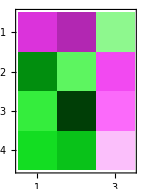

```mathematica
data["X"];
data["Y"];
(A=PLSR[%%,%,4])//MatrixForm
MatrixPlot[%,ColorFunction->"GreenPinkTones"]
```

### Решение (встроенное)

#### Решение (встроенное)

{(ⅆ x_1)/ⅆt=x_1(b_1+∑_(i=1)^3 A_(i,1)x_i)
(ⅆ x_2)/ⅆt=x_2(b_2+∑_(i=1)^3 A_(i,2)x_i)
(ⅆ x_3)/ⅆt=x_3(b_3+∑_(i=1)^3 A_(i,3)x_i)

```mathematica
NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),{x1[1],x2[1],x3[1]}==Rest@First[data["X"]]},{x1[t],x2[t],x3[t]},{t,1,20}];
Nsolution=With[{$=Through[First[%[[All,All,2,0]]][#]]},$&]
```

{InterpolatingFunction[…][#1],InterpolatingFunction[…][#1],InterpolatingFunction[…][#1]}&

#### Graph

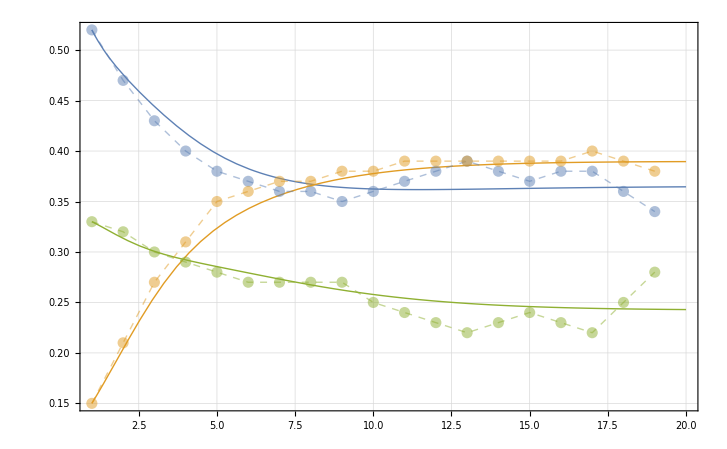

```mathematica
Show[
Plot[Evaluate[Nsolution[t]],{t,1,20},PlotRange->{{1,All},{0,All}},Frame->True,GridLines->Automatic,PlotStyle->Directive[Thick]],
ListPlot[Transpose[dataRaw["X"]],Joined->True,PlotStyle->Directive[Dashed,Thick,Opacity[0.5]],Mesh->All]
]
```

### Решение (в точках)

#### Решение (в точках)

{(Ln[x_1^(k+1)]-Ln[x_1^(k)])/Δt=b_1+∑_(i=1)^3 A_(i,1)x_i^(k)
(Ln[x_2^(k+1)]-Ln[x_2^(k)])/Δt=b_2+∑_(i=1)^3 A_(i,2)x_i^(k)
(Ln[x_3^(k+1)]-Ln[x_3^(k)])/Δt=b_3+∑_(i=1)^3 A_(i,3)x_i^(k)

{Ln[x_1^(k+1)]-Ln[x_1^(k)]=Δt(b_1+∑_(i=1)^3 A_(i,1)x_i^(k))
Ln[x_2^(k+1)]-Ln[x_2^(k)]=Δt(b_2+∑_(i=1)^3 A_(i,2)x_i^(k))
Ln[x_3^(k+1)]-Ln[x_3^(k)]=Δt(b_3+∑_(i=1)^3 A_(i,3)x_i^(k))

{x_1^(k+1)=Exp[Ln[x_1^(k)]+Δt(b_1+∑_(i=1)^3 A_(i,1)x_i^(k))]
x_2^(k+1)=Exp[Ln[x_2^(k)]+Δt(b_2+∑_(i=1)^3 A_(i,2)x_i^(k))]
x_3^(k+1)=Exp[Ln[x_3^(k)]+Δt(b_3+∑_(i=1)^3 A_(i,3)x_i^(k))], k=0,1,…

```mathematica
ClearAll[solution]
solution[1]=Rest[First[data["X"]]]
solution[k_Integer]:=solution[k]=Exp[Log[solution[k-1]]+1Prepend[solution[k-1],1].A]
```

{0.52,0.15,0.33}

```mathematica
dataRaw["X"]
```

{{0.52,0.15,0.33},{0.47,0.21,0.32},{0.43,0.27,0.3},{0.4,0.31,0.29},{0.38,0.35,0.28},{0.37,0.36,0.27},{0.36,0.37,0.27},{0.36,0.37,0.27},{0.35,0.38,0.27},{0.36,0.38,0.25},{0.37,0.39,0.24},{0.38,0.39,0.23},{0.39,0.39,0.22},{0.38,0.39,0.23},{0.37,0.39,0.24},{0.38,0.39,0.23},{0.38,0.4,0.22},{0.36,0.39,0.25},{0.34,0.38,0.28}}

Воспользуемся тем, что Δt=const

```mathematica
solution/@Range[20]
```

{{0.463087,0.210035,0.315598},{0.436912,0.274124,0.29665},{0.406149,0.316065,0.290502},{0.381632,0.33919,0.286097},{0.368124,0.354944,0.278757},{0.361841,0.366453,0.270605},{0.359479,0.374582,0.263304},{0.359139,0.380125,0.257377},{0.359751,0.383799,0.252825},{0.360715,0.386176,0.249462},{0.361716,0.387677,0.247053},{0.362605,0.388599,0.245374},{0.363329,0.389149,0.244235},{0.363884,0.389463,0.243483},{0.364292,0.389634,0.243},{0.364581,0.389719,0.2427},{0.364778,0.389754,0.242521},{0.364909,0.389764,0.242418},{0.364993,0.38976,0.242364},{0.365045,0.389751,0.242338}}

#### Graph

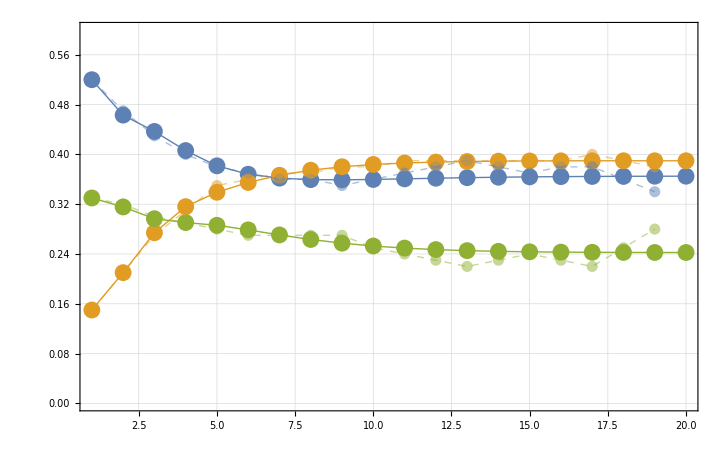

```mathematica
Show[
ListLinePlot[#,PlotRange->{{1,All},{0,0.6}},Frame->True,GridLines->Automatic,PlotStyle->Directive[Thick],Mesh->All],
ListPlot[Transpose[dataRaw["X"]],Joined->True,PlotStyle->Directive[Dashed,Thick,Opacity[0.5]],Mesh->All]
]&[Transpose[solution/@Range[20]]]
```

## Метод Трапеции

## Замена

Применим метод Трапеции

{(Ln[x_1^(k+1)]-Ln[x_1^(k)])/Δt=b_1+∑_(i=1)^3 A_(i,1)(x_i^(k+1)+x_i^(k))/2
(Ln[x_2^(k+1)]-Ln[x_2^(k)])/Δt=b_2+∑_(i=1)^3 A_(i,2)(x_i^(k+1)+x_i^(k))/2
(Ln[x_3^(k+1)]-Ln[x_3^(k)])/Δt=b_3+∑_(i=1)^3 A_(i,3)(x_i^(k+1)+x_i^(k))/2, k=OverBar[1,N-1]

N – количество доступных наблюдений

Определим матрицы X,Y,A:

X_k=[1,(x_1^(k+1)+x_1^(k))/2,(x_2^(k+1)+x_2^(k))/2,(x_3^(k+1)+x_3^(k))/2]– k-ая строка матрицы X

Y_k=[(Ln[x_1^(k+1)]-Ln[x_1^(k)])/Δt,(Ln[x_2^(k+1)]-Ln[x_2^(k)])/Δt,(Ln[x_3^(k+1)]-Ln[x_3^(k)])/Δt]– k-ая строка матрицы Y

k=OverBar[1,N-1]

A=(b_1 | b_2 | b_3
A_(1,1) | A_(1,2) | A_(1,3)
A_(2,1) | A_(2,2) | A_(2,3)
A_(3,1) | A_(3,2) | A_(3,3))

Тогда система примет вид

Y=X.A

## Подготовка данных

### data

```mathematica
data=Join[dataRaw,
<|"X"->(Most[#]+Rest[#])/2&[Join[Transpose@{ConstantArray[1,dataRaw["N"]]},dataRaw["X"],2]],
"Δt"->Differences[dataRaw["t"]],
"Y"->Differences[Map[Log,dataRaw["X"],{2}]]/Differences[dataRaw["t"]]
|>]
```

<|names→{Competitor_X,Competitor_Y,Competitor_Z},X→{{1,0.495,0.18,0.325},{1,0.45,0.24,0.31},{1,0.415,0.29,0.295},{1,0.39,0.33,0.285},{1,0.375,0.355,0.275},{1,0.365,0.365,0.27},{1,0.36,0.37,0.27},{1,0.355,0.375,0.27},{1,0.355,0.38,0.26},{1,0.365,0.385,0.245},{1,0.375,0.39,0.235},{1,0.385,0.39,0.225},{1,0.385,0.39,0.225},{1,0.375,0.39,0.235},{1,0.375,0.39,0.235},{1,0.38,0.395,0.225},{1,0.37,0.395,0.235},{1,0.35,0.385,0.265}},t→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19},N→19,Δt→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},Y→{{-0.101096,0.336472,-0.0307717},{-0.0889475,0.251314,-0.0645385},{-0.0723207,0.13815,-0.0339016},{-0.0512933,0.121361,-0.0350913},{-0.0266682,0.0281709,-0.0363676},{-0.027399,0.027399,0.},{0.,0.,0.},{-0.0281709,0.0266682,0.},{0.0281709,0.,-0.076961},{0.027399,0.0259755,-0.040822},{0.0266682,0.,-0.0425596},{0.0259755,0.,-0.0444518},{-0.0259755,0.,0.0444518},{-0.0266682,0.,0.0425596},{0.0266682,0.,-0.0425596},{0.,0.0253178,-0.0444518},{-0.0540672,-0.0253178,0.127833},{-0.0571584,-0.0259755,0.113329}}|>

## Обычный подход

```mathematica
data["X"];
data["Y"];
N@Inverse[Transpose[%%].%%].Transpose[%%].%//MatrixForm
```

(4.34317 | 0.573392 | -3.61696
-4.40685 | 0.329793 | 3.42591
-4.05951 | -1.58478 | 3.81692
-4.72698 | -0.328493 | 3.59112)

```mathematica
N@LeastSquares[data["X"],data["Y"]]//MatrixForm
```

(4.34317 | 0.573392 | -3.61696
-4.40685 | 0.329793 | 3.42591
-4.05951 | -1.58478 | 3.81692
-4.72698 | -0.328493 | 3.59112)

## Principle Components Regression (PCR)

### PCR

```mathematica
PCR[data["X"],data["Y"],#]&/@Range[4];
Grid[Join[{{"A","||δy||"}},{MatrixForm[#],MatrixForm[Norm[data["Y"]-data["X"].#]/Norm[data["Y"]]]}&/@%],Frame->All]
```

A | ||δy||
(-0.0175685 | 0.0384216 | -0.0067888
-0.00675379 | 0.0147703 | -0.0026098
-0.00624275 | 0.0136527 | -0.00241232
-0.00457193 | 0.00999866 | -0.00176668) | 0.875093
(-0.0235336 | 0.0570527 | -0.0101565
-0.202875 | 0.627325 | -0.113334
0.335508 | -1.05375 | 0.19053
-0.158577 | 0.49101 | -0.0887135) | 0.495541
(-0.043259 | 0.0329178 | -0.00116727
-0.00251503 | 0.872474 | -0.204642
0.345052 | -1.04208 | 0.186181
-0.391788 | 0.205668 | 0.0175649) | 0.493183
(4.34317 | 0.573392 | -3.61696
-4.40685 | 0.329793 | 3.42591
-4.05951 | -1.58478 | 3.81692
-4.72698 | -0.328493 | 3.59112) | 0.482945

## Partial least squares regression (PLSR)

### PLSR

```mathematica
data["X"];
data["Y"];
PLSR[%%,%,#]&/@Range[4];
Grid[Join[{{"A","||δy||"}},{MatrixForm[#],MatrixForm[Norm[%%-%%%.#]/Norm[%%]]}&/@%],Frame->All]
```

A | ||δy||
(-0.0177483 | 0.0389572 | -0.00688537
-0.00785743 | 0.0172469 | -0.00304825
-0.00450466 | 0.00988766 | -0.00174756
-0.00539977 | 0.0118524 | -0.00209482) | 0.871913
(-0.0231347 | 0.0558238 | -0.00993528
-0.206597 | 0.639566 | -0.11558
0.335064 | -1.05341 | 0.190524
-0.154005 | 0.477183 | -0.0862386) | 0.495493
(-0.0333438 | 0.044238 | -0.005453
-0.0112494 | 0.861255 | -0.201346
0.335028 | -1.05345 | 0.19054
-0.403299 | 0.194273 | 0.023213) | 0.493145
(4.34317 | 0.573392 | -3.61696
-4.40685 | 0.329793 | 3.42591
-4.05951 | -1.58478 | 3.81692
-4.72698 | -0.328493 | 3.59112) | 0.482945

## Решение

### A

(4.34317 | 0.573392 | -3.61696
-4.40685 | 0.329793 | 3.42591
-4.05951 | -1.58478 | 3.81692
-4.72698 | -0.328493 | 3.59112)

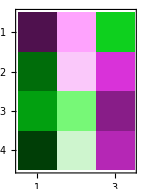

```mathematica
data["X"];
data["Y"];
(A=PLSR[%%,%,4])//MatrixForm
MatrixPlot[%,ColorFunction->"GreenPinkTones"]
```

### Решение (встроенное)

#### Решение (встроенное)

{(ⅆ X_1)/ⅆt=x_1(b_1+∑_(i=1)^3 A_(i,1)x_i)
(ⅆ x_2)/ⅆt=x_2(b_2+∑_(i=1)^3 A_(i,2)x_i)
(ⅆ x_3)/ⅆt=x_3(b_3+∑_(i=1)^3 A_(i,3)x_i)

```mathematica
NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),{x1[1],x2[1],x3[1]}==First[dataRaw["X"]]},{x1[t],x2[t],x3[t]},{t,1,20}];
Nsolution=With[{$=Through[First[%[[All,All,2,0]]][#]]},$&]
```

{InterpolatingFunction[…][#1],InterpolatingFunction[…][#1],InterpolatingFunction[…][#1]}&

#### Graph

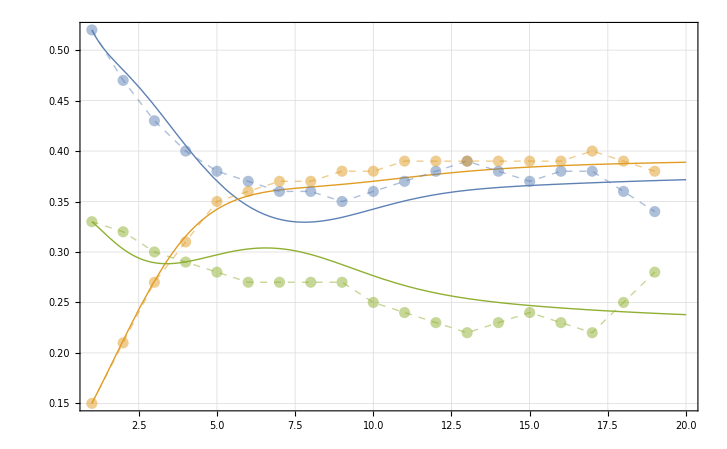

```mathematica
Show[
Plot[Evaluate[Nsolution[t]],{t,1,20},PlotRange->{{1,All},{0,All}},Frame->True,GridLines->Automatic,PlotStyle->Directive[Thick]],
ListPlot[Transpose[dataRaw["X"]],Joined->True,PlotStyle->Directive[Dashed,Thick,Opacity[0.5]],Mesh->All]
]
```

### Решение (в точках) (нужно доделать)

#### Решение (в точках)

{(Ln[x_1^(k+1)]-Ln[x_1^(k)])/Δt=b_1+∑_(i=1)^3 A_(i,1)(x_i^(k+1)+x_i^(k))/2
(Ln[x_2^(k+1)]-Ln[x_2^(k)])/Δt=b_2+∑_(i=1)^3 A_(i,2)(x_i^(k+1)+x_i^(k))/2
(Ln[x_3^(k+1)]-Ln[x_3^(k)])/Δt=b_3+∑_(i=1)^3 A_(i,3)(x_i^(k+1)+x_i^(k))/2

{Ln[x_1^(k+1)]-Ln[x_1^(k)]=Δt(b_1+∑_(i=1)^3 A_(i,1)(x_i^(k+1)+x_i^(k))/2)
Ln[x_2^(k+1)]-Ln[x_2^(k)]=Δt(b_2+∑_(i=1)^3 A_(i,2)(x_i^(k+1)+x_i^(k))/2)
Ln[x_3^(k+1)]-Ln[x_3^(k)]=Δt(b_3+∑_(i=1)^3 A_(i,3)(x_i^(k+1)+x_i^(k))/2)

{2Ln[x_1^(k+1)]-Δt∑_(i=1)^3 A_(i,1)x_i^(k+1)=2Ln[x_1^(k)]+Δt(2 b_1+∑_(i=1)^3 A_(i,1)x_i^(k))
2Ln[x_2^(k+1)]-Δt∑_(i=1)^3 A_(i,2)x_i^(k+1)=2Ln[x_2^(k)]+Δt(2 b_2+∑_(i=1)^3 A_(i,2)x_i^(k))
2Ln[x_3^(k+1)]-Δt∑_(i=1)^3 A_(i,3)x_i^(k+1)=2Ln[x_3^(k)]+Δt(2 b_3+∑_(i=1)^3 A_(i,3)x_i^(k))

```mathematica
ClearAll[solution]
solution[1]=First[dataRaw["X"]]
solution[k_Integer]:=solution[k]=Exp[Log[solution[k-1]]+1Prepend[solution[k-1],1].A]
```

{0.52,0.15,0.33}

Воспользуемся тем, что Δt=const

```mathematica
solution/@Range[20]
```

{{0.52,0.15,0.33},{0.46248,0.223497,0.305277},{0.442024,0.293195,0.280909},{0.390925,0.344839,0.288096},{0.339418,0.366596,0.309953},{0.305299,0.367527,0.32853},{0.291231,0.361587,0.332358},{0.297364,0.356997,0.317562},{0.322901,0.35749,0.288729},{0.358341,0.364162,0.25882},{0.381358,0.375039,0.241351},{0.381068,0.384734,0.238415},{0.371674,0.389,0.241589},{0.365817,0.389049,0.243707},{0.365714,0.388047,0.242843},{0.368771,0.38776,0.240228},{0.371875,0.388373,0.237636},{0.373538,0.389339,0.235937},{0.374003,0.390142,0.235021},{0.374104,0.390627,0.234427}}

#### Graph

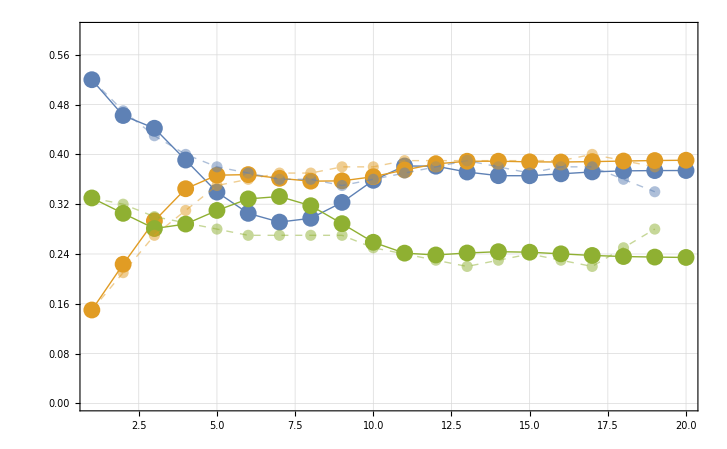

```mathematica
Show[
ListLinePlot[#,PlotRange->{{1,All},{0,0.6}},Frame->True,GridLines->Automatic,PlotStyle->Directive[Thick],Mesh->All],
ListPlot[Transpose[dataRaw["X"]],Joined->True,PlotStyle->Directive[Dashed,Thick,Opacity[0.5]],Mesh->All]
]&[Transpose[solution/@Range[20]]]
```

# MicrobiotaExperiment 2021

## Task

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danila/Documents/Thesis

```mathematica
dataRaw=First@Import["./data/MicrobiotaExperiment 2021.xlsx"];
```

### preData

```mathematica
dataRaw[[{1,2,4,3,5}]];
preData=<|"title"->%[[1,1]],"names"->%[[3;;,1]],"X"->Transpose[%[[3;;,2;;]]],"t"->#,"N"->Length[#]|>&[%[[2,2;;]]]
```

<|title→Эксперимент по кокультивированию клеток с конкурентными микроорганизмами,names→{Эпителиальные клетки,Патологический микрорганизм,Антагонистичный (противопатологический организм)},X→{{10.,10.,10.},{9.98927,10.0924,10.001},{9.97773,10.1851,10.0021},{9.96537,10.2783,10.0033},{9.95219,10.3717,10.0046},{9.9382,10.4655,10.0061},{9.92339,10.5594,10.0077},{9.90777,10.6536,10.0094},{9.89134,10.7479,10.0112},{9.8741,10.8423,10.0131},{9.85605,10.9367,10.0152},{9.8372,11.0312,10.0174},{9.81756,11.1256,10.0197},{9.79712,11.2198,10.0221},{9.77591,11.314,10.0246},{9.75393,11.4079,10.0273},{9.73118,11.5015,10.0301},{9.70767,11.5948,10.033},{9.68341,11.6878,10.036},{9.65841,11.7803,10.0392},{9.63268,11.8723,10.0425},{9.60622,11.9638,10.0459},{9.57906,12.0546,10.0494},{9.55118,12.1448,10.053},{9.52262,12.2342,10.0567},{9.49339,12.3228,10.0606},{9.4635,12.4105,10.0646},{9.43297,12.4973,10.0687},{9.40182,12.5832,10.0729},{9.37005,12.668,10.0772},{9.33769,12.7517,10.0816},{9.30475,12.8342,10.0861},{9.27125,12.9155,10.0908},{9.2372,12.9955,10.0955},{9.20261,13.0742,10.1004},{9.16751,13.1514,10.1053},{9.13192,13.2272,10.1104},{9.09585,13.3014,10.1155},{9.05933,13.3741,10.1208},{9.02237,13.4451,10.1261},{8.98501,13.5144,10.1316},{8.94725,13.582,10.1371},{8.90913,13.6477,10.1427},{8.87065,13.7116,10.1485},{8.83184,13.7736,10.1542},{8.79271,13.8337,10.1601},{8.75328,13.8917,10.1661},{8.71359,13.9477,10.1721},{8.67365,14.0016,10.1782},{8.63349,14.0534,10.1844},{8.59313,14.103,10.1907},{8.55258,14.1504,10.197},{8.51187,14.1956,10.2034},{8.47103,14.2385,10.2098},{8.43007,14.2791,10.2163},{8.389,14.3173,10.2229},{8.34786,14.3532,10.2295},{8.30666,14.3868,10.2362},{8.26542,14.4179,10.2429},{8.22416,14.4466,10.2497},{8.18291,14.4728,10.2565},{8.14169,14.4966,10.2633},{8.10051,14.518,10.2702},{8.0594,14.5368,10.2771},{8.01837,14.5532,10.284},{7.97743,14.5671,10.2909},{7.93662,14.5785,10.2979},{7.89594,14.5874,10.3049},{7.85542,14.5939,10.3119},{7.81506,14.5978,10.3189},{7.7749,14.5993,10.3259},{7.73494,14.5984,10.333},{7.6952,14.5949,10.34},{7.6557,14.5891,10.347},{7.61645,14.5808,10.3541},{7.57746,14.5701,10.3611},{7.53876,14.557,10.3681},{7.50035,14.5416,10.3751},{7.46224,14.5239,10.3821},{7.42446,14.5038,10.389},{7.387,14.4815,10.396},{7.34989,14.4569,10.4029},{7.31313,14.4301,10.4097},{7.27674,14.4011,10.4166},{7.24073,14.3699,10.4234},{7.2051,14.3367,10.4302},{7.16987,14.3013,10.4369},{7.13504,14.264,10.4436},{7.10063,14.2246,10.4502},{7.06663,14.1833,10.4568},{7.03307,14.1401,10.4633},{6.99994,14.095,10.4698},{6.96725,14.048,10.4762},{6.93502,13.9993,10.4826},{6.90324,13.9488,10.4889},{6.87192,13.8967,10.4951},{6.84107,13.8429,10.5013},{6.8107,13.7875,10.5074},{6.78079,13.7306,10.5134},{6.75137,13.6722,10.5194},{6.72243,13.6123,10.5252},{6.69398,13.551,10.531},{6.66602,13.4884,10.5367},{6.63855,13.4244,10.5424},{6.61158,13.3592,10.5479},{6.5851,13.2928,10.5534},{6.55913,13.2253,10.5588},{6.53366,13.1566,10.5641},{6.50869,13.0869,10.5692},{6.48422,13.0161,10.5743},{6.46026,12.9444,10.5794},{6.4368,12.8718,10.5843},{6.41385,12.7983,10.5891},{6.3914,12.7239,10.5938},{6.36946,12.6488,10.5984},{6.34802,12.573,10.6029},{6.32709,12.4965,10.6074},{6.30666,12.4194,10.6117},{6.28673,12.3416,10.6159},{6.2673,12.2633,10.62},{6.24837,12.1845,10.624},{6.22994,12.1052,10.6279},{6.21201,12.0255,10.6317},{6.19457,11.9454,10.6354},{6.17763,11.865,10.6389},{6.16117,11.7843,10.6424},{6.14521,11.7033,10.6457},{6.12973,11.6221,10.649},{6.11474,11.5407,10.6521},{6.10023,11.4591,10.6551},{6.0862,11.3774,10.6581},{6.07264,11.2956,10.6609},{6.05956,11.2138,10.6636},{6.04695,11.1319,10.6661},{6.03481,11.0501,10.6686},{6.02314,10.9683,10.671},{6.01193,10.8865,10.6732},{6.00118,10.8049,10.6754},{5.99089,10.7234,10.6774},{5.98105,10.6421,10.6793},{5.97166,10.5609,10.6811},{5.96272,10.48,10.6828},{5.95422,10.3993,10.6844},{5.94617,10.3188,10.6859},{5.93855,10.2387,10.6872},{5.93137,10.1588,10.6885},{5.92462,10.0793,10.6896},{5.9183,10.0001,10.6907},{5.9124,9.92129,10.6916},{5.90693,9.84287,10.6924},{5.90187,9.76486,10.6931},{5.89723,9.68727,10.6937},{5.893,9.61012,10.6942},{5.88918,9.53343,10.6946},{5.88577,9.45722,10.6949},{5.88276,9.3815,10.6951},{5.88015,9.30628,10.6952},{5.87794,9.23158,10.6952},{5.87611,9.15741,10.6951},{5.87468,9.08379,10.6949},{5.87363,9.01072,10.6945},{5.87296,8.93823,10.6941},{5.87268,8.86631,10.6936},{5.87277,8.79498,10.693},{5.87323,8.72424,10.6923},{5.87407,8.65411,10.6915},{5.87528,8.5846,10.6905},{5.87685,8.51572,10.6895},{5.87878,8.44746,10.6885},{5.88107,8.37985,10.6873},{5.88372,8.31288,10.686},{5.88672,8.24656,10.6846},{5.89007,8.18089,10.6832},{5.89376,8.11589,10.6816},{5.8978,8.05155,10.68},{5.90217,7.98789,10.6782},{5.90689,7.9249,10.6764},{5.91194,7.86259,10.6745},{5.91733,7.80096,10.6726},{5.92305,7.74002,10.6705},{5.9291,7.67977,10.6683},{5.93547,7.6202,10.6661},{5.94216,7.56133,10.6638},{5.94917,7.50315,10.6614},{5.9565,7.44566,10.659},{5.96414,7.38888,10.6564},{5.97209,7.33278,10.6538},{5.98035,7.27739,10.6511},{5.98892,7.22269,10.6483},{5.9978,7.16869,10.6455},{6.00698,7.1154,10.6426},{6.01645,7.0628,10.6396},{6.02623,7.0109,10.6365},{6.0363,6.95969,10.6334},{6.04666,6.90918,10.6302},{6.0573,6.85936,10.627},{6.06824,6.81023,10.6236},{6.07946,6.7618,10.6202},{6.09097,6.71406,10.6168},{6.10275,6.667,10.6133},{6.11482,6.62064,10.6097},{6.12716,6.57496,10.606},{6.13978,6.52997,10.6023},{6.15268,6.48566,10.5986},{6.16583,6.44202,10.5947},{6.17926,6.39906,10.5909},{6.19295,6.35678,10.5869},{6.20691,6.31517,10.5829},{6.22112,6.27422,10.5789},{6.2356,6.23395,10.5748},{6.25033,6.19434,10.5706},{6.26532,6.15539,10.5664},{6.28057,6.1171,10.5622},{6.29606,6.07947,10.5579},{6.31181,6.0425,10.5535},{6.3278,6.00617,10.5491},{6.34404,5.97049,10.5447},{6.36051,5.93546,10.5402},{6.37723,5.90107,10.5357},{6.39419,5.86731,10.5311},{6.41138,5.8342,10.5265},{6.42882,5.80172,10.5218},{6.44648,5.76987,10.5171},{6.46438,5.73865,10.5123},{6.4825,5.70806,10.5076},{6.50086,5.67809,10.5027},{6.51944,5.64873,10.4979},{6.53824,5.62,10.493},{6.55726,5.59188,10.488},{6.5765,5.56437,10.4831},{6.59596,5.53747,10.4781},{6.61563,5.51118,10.473},{6.63551,5.48549,10.468},{6.65561,5.4604,10.4629},{6.67592,5.43591,10.4577},{6.69644,5.41203,10.4526},{6.71716,5.38873,10.4474},{6.73808,5.36603,10.4421},{6.75921,5.34392,10.4369},{6.78053,5.32239,10.4316},{6.80204,5.30145,10.4263},{6.82376,5.2811,10.421},{6.84566,5.26132,10.4157},{6.86776,5.24213,10.4103},{6.89004,5.22351,10.4049},{6.91251,5.20547,10.3995},{6.93516,5.18801,10.394},{6.958,5.17112,10.3886},{6.98101,5.1548,10.3831},{7.0042,5.13906,10.3776},{7.02757,5.12388,10.3721},{7.05111,5.10926,10.3666},{7.07481,5.09522,10.361},{7.09868,5.08174,10.3555},{7.12272,5.06882,10.3499},{7.14692,5.05647,10.3443},{7.17128,5.04469,10.3387},{7.1958,5.03346,10.3331},{7.22047,5.0228,10.3275},{7.2453,5.0127,10.3218},{7.27027,5.00316,10.3162},{7.29539,4.99419,10.3105},{7.32066,4.98577,10.3049},{7.34606,4.97791,10.2992},{7.3716,4.97062,10.2935},{7.39728,4.96388,10.2879},{7.42309,4.95771,10.2822},{7.44903,4.95209,10.2765},{7.4751,4.94705,10.2708},{7.50129,4.94256,10.2651},{7.5276,4.93864,10.2594},{7.55403,4.93528,10.2537},{7.58057,4.93249,10.248},{7.60722,4.93027,10.2423},{7.63398,4.92862,10.2366},{7.66084,4.92753,10.2309},{7.6878,4.92701,10.2252},{7.71486,4.92707,10.2195},{7.74201,4.9277,10.2138},{7.76925,4.92891,10.2081},{7.79657,4.93069,10.2024},{7.82398,4.93306,10.1967},{7.85147,4.936,10.191},{7.87902,4.93954,10.1854},{7.90665,4.94366,10.1797},{7.93434,4.94837,10.1741},{7.9621,4.95367,10.1684},{7.98991,4.95957,10.1628},{8.01778,4.96607,10.1572},{8.04569,4.97317,10.1516},{8.07365,4.98087,10.146},{8.10164,4.98919,10.1404},{8.12967,4.99811,10.1349},{8.15773,5.00765,10.1293},{8.18582,5.0178,10.1238},{8.21392,5.02858,10.1183},{8.24203,5.03999,10.1128},{8.27016,5.05203,10.1073},{8.29829,5.06471,10.1018},{8.32642,5.07802,10.0964},{8.35454,5.09198,10.091},{8.38265,5.10659,10.0856},{8.41075,5.12186,10.0802},{8.43882,5.13778,10.0748},{8.46686,5.15437,10.0695},{8.49487,5.17162,10.0642},{8.52283,5.18955,10.0589},{8.55075,5.20816,10.0536},{8.57861,5.22745,10.0484},{8.60641,5.24743,10.0432},{8.63414,5.26811,10.038},{8.66179,5.28949,10.0329},{8.68936,5.31158,10.0278},{8.71685,5.33438,10.0227},{8.74424,5.35791,10.0177},{8.77154,5.38216,10.0127},{8.79873,5.40715,10.0077},{8.8258,5.43288,10.0027},{8.85275,5.45935,9.99782},{8.87957,5.48657,9.99295},{8.90625,5.51455,9.98811},{8.93278,5.5433,9.98331},{8.95916,5.57282,9.97856},{8.98537,5.60311,9.97384},{9.0114,5.63419,9.96917},{9.03726,5.66607,9.96453},{9.06292,5.69874,9.95995},{9.08838,5.73222,9.9554},{9.11365,5.76652,9.9509},{9.13871,5.80163,9.94645},{9.16354,5.83758,9.94204}},t→{0.,0.04,0.08,0.12,0.16,0.2,0.24,0.28,0.32,0.36,0.4,0.44,0.48,0.52,0.56,0.6,0.64,0.68,0.72,0.76,0.8,0.84,0.88,0.92,0.96,1.,1.04,1.08,1.12,1.16,1.2,1.24,1.28,1.32,1.36,1.4,1.44,1.48,1.52,1.56,1.6,1.64,1.68,1.72,1.76,1.8,1.84,1.88,1.92,1.96,2.,2.04,2.08,2.12,2.16,2.2,2.24,2.28,2.32,2.36,2.4,2.44,2.48,2.52,2.56,2.6,2.64,2.68,2.72,2.76,2.8,2.84,2.88,2.92,2.96,3.,3.04,3.08,3.12,3.16,3.2,3.24,3.28,3.32,3.36,3.4,3.44,3.48,3.52,3.56,3.6,3.64,3.68,3.72,3.76,3.8,3.84,3.88,3.92,3.96,4.,4.04,4.08,4.12,4.16,4.2,4.24,4.28,4.32,4.36,4.4,4.44,4.48,4.52,4.56,4.6,4.64,4.68,4.72,4.76,4.8,4.84,4.88,4.92,4.96,5.,5.04,5.08,5.12,5.16,5.2,5.24,5.28,5.32,5.36,5.4,5.44,5.48,5.52,5.56,5.6,5.64,5.68,5.72,5.76,5.8,5.84,5.88,5.92,5.96,6.,6.04,6.08,6.12,6.16,6.2,6.24,6.28,6.32,6.36,6.4,6.44,6.48,6.52,6.56,6.6,6.64,6.68,6.72,6.76,6.8,6.84,6.88,6.92,6.96,7.,7.04,7.08,7.12,7.16,7.2,7.24,7.28,7.32,7.36,7.4,7.44,7.48,7.52,7.56,7.6,7.64,7.68,7.72,7.76,7.8,7.84,7.88,7.92,7.96,8.,8.04,8.08,8.12,8.16,8.2,8.24,8.28,8.32,8.36,8.4,8.44,8.48,8.52,8.56,8.6,8.64,8.68,8.72,8.76,8.8,8.84,8.88,8.92,8.96,9.,9.04,9.08,9.12,9.16,9.2,9.24,9.28,9.32,9.36,9.4,9.44,9.48,9.52,9.56,9.6,9.64,9.68,9.72,9.76,9.8,9.84,9.88,9.92,9.96,10.,10.04,10.08,10.12,10.16,10.2,10.24,10.28,10.32,10.36,10.4,10.44,10.48,10.52,10.56,10.6,10.64,10.68,10.72,10.76,10.8,10.84,10.88,10.92,10.96,11.,11.04,11.08,11.12,11.16,11.2,11.24,11.28,11.32,11.36,11.4,11.44,11.48,11.52,11.56,11.6,11.64,11.68,11.72,11.76,11.8,11.84,11.88,11.92,11.96,12.,12.04,12.08,12.12,12.16,12.2,12.24,12.28,12.32,12.36,12.4,12.44,12.48,12.52,12.56,12.6,12.64,12.68,12.72,12.76,12.8,12.84,12.88,12.92,12.96,13.,13.04,13.08,13.12,13.16,13.2},N→331|>

## Model

{(ⅆ x_1)/ⅆt=x_1(b_1+∑_(i=1)^3 A_(i,1)x_i)
(ⅆ x_2)/ⅆt=x_2(b_2+∑_(i=1)^3 A_(i,2)x_i)
(ⅆ x_3)/ⅆt=x_3(b_3+∑_(i=1)^3 A_(i,3)x_i)

{ⅆLn[x_1]/ⅆt=b_1+∑_(i=1)^3 A_(i,1)x_i
ⅆLn[x_2]/ⅆt=b_2+∑_(i=1)^3 A_(i,2)x_i
ⅆLn[x_3]/ⅆt=b_3+∑_(i=1)^3 A_(i,3)x_i

## Метод Эйлера

## Замена

Применим метод Эйлера

{(Ln[x_1^(k+1)]-Ln[x_1^(k)])/Δt=b_1+∑_(i=1)^3 A_(i,1)x_i^(k)
(Ln[x_2^(k+1)]-Ln[x_2^(k)])/Δt=b_2+∑_(i=1)^3 A_(i,2)x_i^(k)
(Ln[x_3^(k+1)]-Ln[x_3^(k)])/Δt=b_3+∑_(i=1)^3 A_(i,3)x_i^(k), k=OverBar[1,N-1]

N – количество доступных наблюдений

Определим матрицы X,Y,A:

X_k=[1,x_1^(k),x_2^(k),x_3^(k)]– k-ая строка матрицы X

Y_k=[(Ln[x_1^(k+1)]-Ln[x_1^(k)])/Δt,(Ln[x_2^(k+1)]-Ln[x_2^(k)])/Δt,(Ln[x_3^(k+1)]-Ln[x_3^(k)])/Δt]– k-ая строка матрицы Y

k=OverBar[1,N-1]

A=(b_1 | b_2 | b_3
A_(1,1) | A_(1,2) | A_(1,3)
A_(2,1) | A_(2,2) | A_(2,3)
A_(3,1) | A_(3,2) | A_(3,3))

Тогда система примет вид

Y=X.A

## Подготовка данных

### data

```mathematica
data=Join[preData,
<|"X"->Most@Join[Transpose@{ConstantArray[1,preData["N"]]},preData["X"],2],
"Δt"->Differences[preData["t"]],
"Y"->Differences[Map[Log,preData["X"],{2}]]/Differences[preData["t"]]
|>];
```

## Подходы

### Обычный подход

```mathematica
data["X"];
data["Y"];
N@Inverse[Transpose[%%].%%].Transpose[%%].%//MatrixForm
```

(0.226628 | -0.0280342 | -0.0337612
-0.000868391 | 0.0933654 | 0.000124056
-0.0223593 | -0.000334157 | 0.00319419
-0.00214558 | -0.0672646 | 0.000306511)

```mathematica
N@LeastSquares[data["X"],data["Y"]]//MatrixForm
```

(0.226628 | -0.0280342 | -0.0337612
-0.000868391 | 0.0933654 | 0.000124056
-0.0223593 | -0.000334157 | 0.00319419
-0.00214558 | -0.0672646 | 0.000306511)

### Principle Components Regression (PCR)

```mathematica
PCR[data["X"],data["Y"],#]&/@Range[4];
Grid[Join[{{"A","||δy||"}},{MatrixForm[#],MatrixForm[Norm[data["Y"]-data["X"].#]/Norm[data["Y"]]]}&/@%],Frame->All]
```

A | ||δy||
(-0.0000709792 | -0.000136218 | 4.75304×10^-6
-0.000527428 | -0.0010122 | 0.0000353186
-0.000686273 | -0.00131704 | 0.0000459555
-0.000736071 | -0.00141261 | 0.0000492902) | 0.972536
(0.00127485 | -0.000238937 | -0.000190815
0.008955 | -0.00173593 | -0.00134261
-0.0226695 | 0.000360799 | 0.00324042
0.0128356 | -0.00244845 | -0.00192285) | 0.967615
(0.00154453 | -0.00441179 | -0.000231133
0.00283418 | 0.0929768 | -0.000427504
-0.0226264 | -0.000306121 | 0.00323398
0.0171552 | -0.0692902 | -0.00256867) | 0.00545046
(0.226628 | -0.0280342 | -0.0337612
-0.000868391 | 0.0933654 | 0.000124056
-0.0223593 | -0.000334157 | 0.00319419
-0.00214558 | -0.0672646 | 0.000306511) | 0.00124679

### Partial least squares regression (PLSR)

```mathematica
data["X"];
data["Y"];
PLSR[%%,%,#]&/@Range[4];
Grid[Join[{{"A","||δy||"}},{MatrixForm[#],MatrixForm[Norm[%%-%%%.#]/Norm[%%]]}&/@%],Frame->All]
```

A | ||δy||
(-0.0000790996 | -0.00014456 | 5.9048×10^-6
-0.000299117 | -0.000546658 | 0.0000223291
-0.000913191 | -0.00166892 | 0.0000681699
-0.000877732 | -0.00160412 | 0.0000655229) | 0.969722
(0.00142301 | -0.000439749 | -0.00021312
0.00573869 | -0.00173318 | -0.000858049
-0.022716 | 0.00261568 | 0.00324726
0.0151762 | -0.00475897 | -0.00227531) | 0.956989
(0.00154484 | -0.00441222 | -0.000231178
0.00283417 | 0.0929768 | -0.000427504
-0.0226264 | -0.000306121 | 0.00323398
0.0171552 | -0.0692902 | -0.00256867) | 0.00545046
(0.226628 | -0.0280342 | -0.0337612
-0.000868391 | 0.0933654 | 0.000124056
-0.0223593 | -0.000334157 | 0.00319419
-0.00214558 | -0.0672646 | 0.000306511) | 0.00124679

## Решение

### A

(0.226628 | -0.0280342 | -0.0337612
-0.000868391 | 0.0933654 | 0.000124056
-0.0223593 | -0.000334157 | 0.00319419
-0.00214558 | -0.0672646 | 0.000306511)

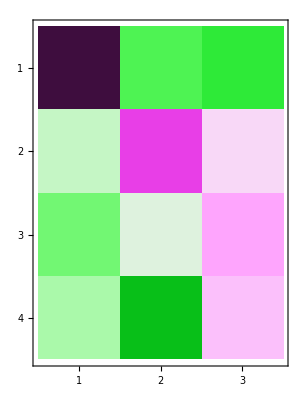

```mathematica
data["X"];
data["Y"];
(A=PLSR[%%,%,4])//MatrixForm
MatrixPlot[%,ColorFunction->"GreenPinkTones"]
```

```mathematica
Grid[Join[Transpose@{Join[{"","const"},data["names"]]},Join[{data["names"]},A],2],Frame->All]
```

| Эпителиальные клетки | Патологический микрорганизм | Антагонистичный (противопатологический организм)
const | 0.226628 | -0.0280342 | -0.0337612
Эпителиальные клетки | -0.000868391 | 0.0933654 | 0.000124056
Патологический микрорганизм | -0.0223593 | -0.000334157 | 0.00319419
Антагонистичный (противопатологический организм) | -0.00214558 | -0.0672646 | 0.000306511

```mathematica
Grid[Join[Transpose@{Join[{"","const"},data["names"]]},Join[{data["names"]},Transpose@kmConfidenceInterval[data["X"],data["Y"],A]],2],Frame->All]
```

| Эпителиальные клетки | Патологический микрорганизм | Антагонистичный (противопатологический организм)
const | 0.22663 (±9.47×10^-6) | -0.02803 (±7.31×10^-6) | -0.03376 (±1.93×10^-7)
Эпителиальные клетки | -0.00087 (±2.61×10^-9) | 0.09337 (±2.02×10^-9) | 0.00012 (±5.33×10^-11)
Патологический микрорганизм | -0.02236 (±2.15×10^-11) | -0.00033 (±1.66×10^-11) | 0.00319 (±4.39×10^-13)
Антагонистичный (противопатологический организм) | -0.00215 (±6.96×10^-8) | -0.06726 (±5.38×10^-8) | 0.00031 (±1.42×10^-9)

```mathematica
kmCoefficientR2[data["X"],data["Y"],A]
```

{0.999997,0.999999,0.999997}

```mathematica
Join[Transpose@kmConfidenceInterval[data["X"],data["Y"],A],Table[StringForm["a_(``, ``)",i,j],{i,0,3},{j,1,3}],2][[All,{4,1,5,2,6,3}]];
{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"};
Grid[Join[Transpose@{Join[{"","Естественный рост"},%]},Join[{Riffle[%,SpanFromLeft,{2,-1,2}]},%%],2],Frame->All,Alignment->{{Center},{Left}}]
(*Export["./Documents/Thesis/res/smoothed-euler.png",%]*)
```

| Эпителиальные клетки X |  | Кандида Y |  | Бактерии стрептококков Z | 
Естественный рост | a_(RowBox[{) | 0.22663 (±9.47×10^-6) | a_(RowBox[{) | -0.02803 (±7.31×10^-6) | a_(RowBox[{) | -0.03376 (±1.93×10^-7)
Эпителиальные клетки X | a_(RowBox[{) | -0.00087 (±2.61×10^-9) | a_(RowBox[{) | 0.09337 (±2.02×10^-9) | a_(RowBox[{) | 0.00012 (±5.33×10^-11)
Кандида Y | a_(RowBox[{) | -0.02236 (±2.15×10^-11) | a_(RowBox[{) | -0.00033 (±1.66×10^-11) | a_(RowBox[{) | 0.00319 (±4.39×10^-13)
Бактерии стрептококков Z | a_(RowBox[{) | -0.00215 (±6.96×10^-8) | a_(RowBox[{) | -0.06726 (±5.38×10^-8) | a_(RowBox[{) | 0.00031 (±1.42×10^-9)

### Сравнение

#### Решение (встроенное)

{(ⅆ x_1)/ⅆt=x_1(b_1+∑_(i=1)^3 A_(i,1)x_i)
(ⅆ x_2)/ⅆt=x_2(b_2+∑_(i=1)^3 A_(i,2)x_i)
(ⅆ x_3)/ⅆt=x_3(b_3+∑_(i=1)^3 A_(i,3)x_i)

```mathematica
NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),{x1[0],x2[0],x3[0]}==Rest@First[data["X"]]},{x1[t],x2[t],x3[t]},{t,preData["t"]//Min,1.25preData["t"]//Max}];
Nsolution=With[{$=Through[First[%[[All,All,2,0]]][#]]},$&]
```

{InterpolatingFunction[…][#1],InterpolatingFunction[…][#1],InterpolatingFunction[…][#1]}&

#### Graph

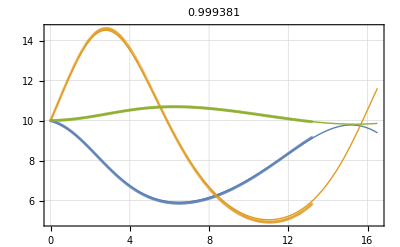

```mathematica
Show[
Plot[Evaluate[Nsolution[t]],{t,preData["t"]//Min,1.25preData["t"]//Max},PlotRange->{{0,All},{0,All}},Frame->True,GridLines->Automatic,PlotStyle->Directive[Thick]],
ListPlot[Transpose[preData["X"]],Joined->True,DataRange->{0,Last[preData["t"]]},PlotStyle->Directive[Dashed,Thick,Opacity[0.5]],Mesh->All],PlotLabel->Mean[kmCoefficientR2Raw[Nsolution,Transpose@preData["X"],preData["t"]]]
]
```

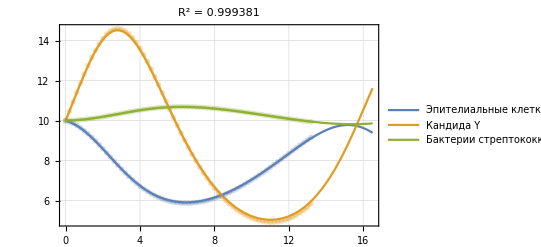

./Documents/Thesis/res/smoothed-euler-plot.png

```mathematica
Show[
Plot[Evaluate[Nsolution[t]],{t,preData["t"]//Min,1.25preData["t"]//Max},PlotRange->{{0,All},{0,All}},Frame->True,GridLines->Automatic,PlotLegends->{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"},PlotStyle->Directive[Thick]],
ListPlot[Transpose[preData["X"][[;;;;5]]],PlotMarkers->{"OpenMarkers"},PlotStyle->Opacity[.3],
DataRange->{0,Last[preData["t"]]},Joined->True],
PlotLabel->StringForm["R^2 = ``",Mean[kmCoefficientR2Raw[Nsolution,Transpose@preData["X"],preData["t"]]]]
]
Export["./Documents/Thesis/res/smoothed-euler-plot.png",%]
```

```mathematica
kmCoefficientR2[data["X"],data["Y"],A]
kmCoefficientR2Raw[Nsolution,Transpose@preData["X"],preData["t"]]
```

{0.999997,0.999999,0.999997}

{0.999468,0.999473,0.999203}

#### infty

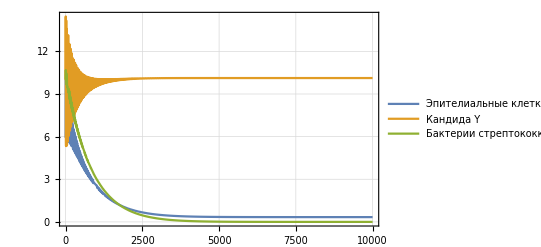

./Documents/Thesis/res/smoothed-euler-semiinfty.png

```mathematica
NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),{x1[0],x2[0],x3[0]}==First[preData["X"]]},{x1[t],x2[t],x3[t]},{t,0.,1. 10^4}];
NsolutionInfty=With[{$=Through[First[%[[All,All,2,0]]][#]]},$&];
Plot[Evaluate[NsolutionInfty[t]],{t,0,1. 10^4},PlotRange->{{0,All},{0,All}},Frame->True,GridLines->Automatic,PlotStyle->Directive[Thick],PlotLegends->{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"}]
Export["./Documents/Thesis/res/smoothed-euler-semiinfty.png",%]
```

```mathematica
NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),{x1[0],x2[0],x3[0]}==First[preData["X"]]},{x1[t],x2[t],x3[t]},{t,1. 10^7,1. 10^7}];
NsolutionInfty=With[{$=Through[First[%[[All,All,2,0]]][#]]},$&];
NsolutionInfty[1. 10^7]
```

{0.336492,10.1227,-3.09423×10^-41}

## Метод Трапеции

## Замена

Применим метод Трапеции

{(Ln[x_1^(k+1)]-Ln[x_1^(k)])/Δt=b_1+∑_(i=1)^3 A_(i,1)(x_i^(k+1)+x_i^(k))/2
(Ln[x_2^(k+1)]-Ln[x_2^(k)])/Δt=b_2+∑_(i=1)^3 A_(i,2)(x_i^(k+1)+x_i^(k))/2
(Ln[x_3^(k+1)]-Ln[x_3^(k)])/Δt=b_3+∑_(i=1)^3 A_(i,3)(x_i^(k+1)+x_i^(k))/2, k=OverBar[1,N-1]

N – количество доступных наблюдений

Определим матрицы X,Y,A:

X_k=[1,(x_1^(k+1)+x_1^(k))/2,(x_2^(k+1)+x_2^(k))/2,(x_3^(k+1)+x_3^(k))/2]– k-ая строка матрицы X

Y_k=[(Ln[x_1^(k+1)]-Ln[x_1^(k)])/Δt,(Ln[x_2^(k+1)]-Ln[x_2^(k)])/Δt,(Ln[x_3^(k+1)]-Ln[x_3^(k)])/Δt]– k-ая строка матрицы Y

k=OverBar[1,N-1]

A=(b_1 | b_2 | b_3
A_(1,1) | A_(1,2) | A_(1,3)
A_(2,1) | A_(2,2) | A_(2,3)
A_(3,1) | A_(3,2) | A_(3,3))

Тогда система примет вид

Y=X.A

## Подготовка данных

### data

```mathematica
data=Join[preData,
<|"X"->(Most[#]+Rest[#])/2&[Join[Transpose@{ConstantArray[1,preData["N"]]},preData["X"],2]],
"Δt"->Differences[preData["t"]],
"Y"->Differences[Map[Log,preData["X"],{2}]]/Differences[preData["t"]]
|>];
```

## Подходы

### Обычный подход

```mathematica
data["X"];
data["Y"];
N@Inverse[Transpose[%%].%%].Transpose[%%].%//MatrixForm
```

(0.198129 | -0.0559291 | -0.0296899
9.16134×10^-7 | 0.0938074 | -1.30876×10^-7
-0.0224005 | -3.81238×10^-7 | 0.00320008
6.65294×10^-6 | -0.0651732 | -9.5042×10^-7)

```mathematica
N@LeastSquares[data["X"],data["Y"]]//MatrixForm
```

(0.198129 | -0.0559291 | -0.0296899
9.16134×10^-7 | 0.0938074 | -1.30876×10^-7
-0.0224005 | -3.81238×10^-7 | 0.00320008
6.65294×10^-6 | -0.0651732 | -9.50421×10^-7)

### Principle Components Regression (PCR)

```mathematica
PCR[data["X"],data["Y"],#]&/@Range[4];
Grid[Join[{{"A","||δy||"}},{MatrixForm[#],MatrixForm[Norm[data["Y"]-data["X"].#]/Norm[data["Y"]]]}&/@%],Frame->All]
```

A | ||δy||
(-0.0000709589 | -0.000135808 | 4.74712×10^-6
-0.000527143 | -0.0010089 | 0.0000352657
-0.000685649 | -0.00131226 | 0.0000458697
-0.000735862 | -0.00140837 | 0.0000492289) | 0.972738
(0.00127315 | -0.000254166 | -0.000190568
0.00897368 | -0.00184551 | -0.00134531
-0.0226683 | 0.00062345 | 0.0032402
0.0128111 | -0.00260127 | -0.0019193) | 0.96727
(0.00152593 | -0.0044342 | -0.000228473
0.00324067 | 0.0929588 | -0.000485614
-0.0226343 | 0.0000608364 | 0.0032351
0.0168619 | -0.069588 | -0.00252675) | 0.00479922
(0.198129 | -0.0559291 | -0.0296899
9.16134×10^-7 | 0.0938074 | -1.30876×10^-7
-0.0224005 | -3.81238×10^-7 | 0.00320008
6.65294×10^-6 | -0.0651732 | -9.50421×10^-7) | 0.0000726457

### Partial least squares regression (PLSR)

```mathematica
data["X"];
data["Y"];
PLSR[%%,%,#]&/@Range[4];
Grid[Join[{{"A","||δy||"}},{MatrixForm[#],MatrixForm[Norm[%%-%%%.#]/Norm[%%]]}&/@%],Frame->All]
```

A | ||δy||
(-0.0000792013 | -0.000144479 | 5.90125×10^-6
-0.000298943 | -0.000545334 | 0.0000222741
-0.000908477 | -0.00165725 | 0.0000676901
-0.000878969 | -0.00160342 | 0.0000654914) | 0.969955
(0.00142819 | -0.000465685 | -0.00021388
0.00558059 | -0.00179818 | -0.000834973
-0.0227065 | 0.00298762 | 0.00324589
0.0152681 | -0.00504413 | -0.00228878) | 0.955978
(0.00152621 | -0.00443482 | -0.000228514
0.00324066 | 0.0929588 | -0.000485614
-0.0226343 | 0.0000608356 | 0.0032351
0.0168619 | -0.069588 | -0.00252675) | 0.00479921
(0.198129 | -0.0559291 | -0.0296899
9.16134×10^-7 | 0.0938074 | -1.30876×10^-7
-0.0224005 | -3.81238×10^-7 | 0.00320008
6.65294×10^-6 | -0.0651732 | -9.50421×10^-7) | 0.0000726457

## Решение

### A

#### A

(0.198129 | -0.0559291 | -0.0296899
9.16134×10^-7 | 0.0938074 | -1.30876×10^-7
-0.0224005 | -3.81238×10^-7 | 0.00320008
6.65294×10^-6 | -0.0651732 | -9.50421×10^-7)

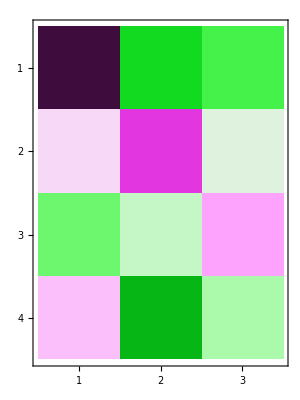

```mathematica
data["X"];
data["Y"];
(A=PLSR[%%,%,4])//MatrixForm
MatrixPlot[%,ColorFunction->"GreenPinkTones"]
```

#### analysis

```mathematica
A
```

{{0.198129,-0.0559291,-0.0296899},{9.16134×10^-7,0.0938074,-1.30876×10^-7},{-0.0224005,-3.81238×10^-7,0.00320008},{6.65294×10^-6,-0.0651732,-9.50421×10^-7}}

```mathematica
MatrixRank[A[[{1,2,3,4},All]]]
```

3

```mathematica
Solve[{1,x1,x2,x3}.A=={0,0,0}]
Solve[{1,x1,x2,0}.A[[All,{1,2}]]=={0,0}]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{6.65294×10^-6,-0.0224005,9.16134×10^-7,0.198129},{-0.0651732,-3.81238×10^-7,0.0938074,-0.0559291},{-9.50421×10^-7,0.00320008,-1.30876×10^-7,-0.0296899}} may contain significant numerical errors.

{{x1→2.53679×10^11,x2→1.1882×10^8,x3→3.65135×10^11}}

{{x1→0.596248,x2→8.84485}}

#### tables

```mathematica
Grid[Join[Transpose@{Join[{"","const"},data["names"]]},Join[{data["names"]},A],2],Frame->All]
```

| Эпителиальные клетки | Патологический микрорганизм | Антагонистичный (противопатологический организм)
const | 0.198129 | -0.0559291 | -0.0296899
Эпителиальные клетки | 9.16134×10^-7 | 0.0938074 | -1.30876×10^-7
Патологический микрорганизм | -0.0224005 | -3.81238×10^-7 | 0.00320008
Антагонистичный (противопатологический организм) | 6.65294×10^-6 | -0.0651732 | -9.50421×10^-7

```mathematica
Grid[Join[Transpose@{Join[{"","const"},data["names"]]},Join[{data["names"]},Transpose@kmConfidenceInterval[data["X"],data["Y"],A]],2],Frame->All]
```

| Эпителиальные клетки | Патологический микрорганизм | Антагонистичный (противопатологический организм)
const | 0.19813 (±3.38×10^-8) | -0.05593 (±3.79×10^-8) | -0.02969 (±6.89×10^-10)
Эпителиальные клетки | 0.00000 (±9.35×10^-12) | 0.09381 (±1.05×10^-11) | -0.00000 (±1.91×10^-13)
Патологический микрорганизм | -0.02240 (±7.65×10^-14) | -0.00000 (±8.58×10^-14) | 0.00320 (±1.56×10^-15)
Антагонистичный (противопатологический организм) | 0.00001 (±2.48×10^-10) | -0.06517 (±2.78×10^-10) | -0.00000 (±5.07×10^-12)

```mathematica
{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"};
Grid[Join[Transpose@{Join[{"","const"},%]},Join[{%},A],2],Frame->All]
```

| Эпителиальные клетки X | Кандида Y | Бактерии стрептококков Z
const | 0.198129 | -0.0559291 | -0.0296899
Эпителиальные клетки X | 9.16134×10^-7 | 0.0938074 | -1.30876×10^-7
Кандида Y | -0.0224005 | -3.81238×10^-7 | 0.00320008
Бактерии стрептококков Z | 6.65294×10^-6 | -0.0651732 | -9.50421×10^-7

```mathematica
Join[A,Table[StringForm["a_(``, ``)",i,j],{i,0,3},{j,1,3}],2][[All,{4,1,5,2,6,3}]];
{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"};
Grid[Join[Transpose@{Join[{"","const"},%]},Join[{Riffle[%,SpanFromLeft,{2,-1,2}]},%%],2],Frame->All]
```

| Эпителиальные клетки X |  | Кандида Y |  | Бактерии стрептококков Z | 
const | a_(RowBox[{) | 0.198129 | a_(RowBox[{) | -0.0559291 | a_(RowBox[{) | -0.0296899
Эпителиальные клетки X | a_(RowBox[{) | 9.16134×10^-7 | a_(RowBox[{) | 0.0938074 | a_(RowBox[{) | -1.30876×10^-7
Кандида Y | a_(RowBox[{) | -0.0224005 | a_(RowBox[{) | -3.81238×10^-7 | a_(RowBox[{) | 0.00320008
Бактерии стрептококков Z | a_(RowBox[{) | 6.65294×10^-6 | a_(RowBox[{) | -0.0651732 | a_(RowBox[{) | -9.50421×10^-7

```mathematica
Join[Transpose@kmConfidenceInterval[data["X"],data["Y"],A],Table[StringForm["a_(``, ``)",i,j],{i,0,3},{j,1,3}],2][[All,{4,1,5,2,6,3}]];
{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"};
Grid[Join[Transpose@{Join[{"","Естественный рост"},%]},Join[{Riffle[%,SpanFromLeft,{2,-1,2}]},%%],2],Frame->All,Alignment->{{Center},{Left}}]
(*Export["./Documents/Thesis/res/smoothed-trapez.png",%]*)
```

| Эпителиальные клетки X |  | Кандида Y |  | Бактерии стрептококков Z | 
Естественный рост | a_(RowBox[{) | 0.19813 (±3.38×10^-8) | a_(RowBox[{) | -0.05593 (±3.79×10^-8) | a_(RowBox[{) | -0.02969 (±6.89×10^-10)
Эпителиальные клетки X | a_(RowBox[{) | 0.00000 (±9.35×10^-12) | a_(RowBox[{) | 0.09381 (±1.05×10^-11) | a_(RowBox[{) | -0.00000 (±1.91×10^-13)
Кандида Y | a_(RowBox[{) | -0.02240 (±7.65×10^-14) | a_(RowBox[{) | -0.00000 (±8.58×10^-14) | a_(RowBox[{) | 0.00320 (±1.56×10^-15)
Бактерии стрептококков Z | a_(RowBox[{) | 0.00001 (±2.48×10^-10) | a_(RowBox[{) | -0.06517 (±2.78×10^-10) | a_(RowBox[{) | -0.00000 (±5.07×10^-12)

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["./Documents/Thesis/res/smoothed-trapez.png"]]]
```

#### system

```mathematica
DecimalForm[Thread[Rule[Flatten@Table[StringForm["a_(````)",i,j],{i,0,3},{j,1,3}],Flatten@A]],{3,3}]
```

{SubscriptBox[a, RowBox[{"\"0\""}]RowBox[{"\"1\""}]]→0.198,SubscriptBox[a, RowBox[{"\"0\""}]RowBox[{"\"2\""}]]→-0.056,SubscriptBox[a, RowBox[{"\"0\""}]RowBox[{"\"3\""}]]→-0.030,SubscriptBox[a, RowBox[{"\"1\""}]RowBox[{"\"1\""}]]→0.000,SubscriptBox[a, RowBox[{"\"1\""}]RowBox[{"\"2\""}]]→0.094,SubscriptBox[a, RowBox[{"\"1\""}]RowBox[{"\"3\""}]]→-0.000,SubscriptBox[a, RowBox[{"\"2\""}]RowBox[{"\"1\""}]]→-0.022,SubscriptBox[a, RowBox[{"\"2\""}]RowBox[{"\"2\""}]]→-0.000,SubscriptBox[a, RowBox[{"\"2\""}]RowBox[{"\"3\""}]]→0.003,SubscriptBox[a, RowBox[{"\"3\""}]RowBox[{"\"1\""}]]→0.000,SubscriptBox[a, RowBox[{"\"3\""}]RowBox[{"\"2\""}]]→-0.065,SubscriptBox[a, RowBox[{"\"3\""}]RowBox[{"\"3\""}]]→-0.000}

Piecewise[{{ⅆX/ⅆt=X(0.198                        -0.022StyleBox[\"\"\",ShowStringCharacters->False]Y), }, {ⅆY/ⅆt=Y(-0.056 "" +0.094X                     -0.065 Z), }, {ⅆZ/ⅆt=Z("-0.03"                        +0.003 Y), }}]

### Сравнение

#### Решение (встроенное)

{(ⅆ X_1)/ⅆt=x_1(b_1+∑_(i=1)^3 A_(i,1)x_i)
(ⅆ x_2)/ⅆt=x_2(b_2+∑_(i=1)^3 A_(i,2)x_i)
(ⅆ x_3)/ⅆt=x_3(b_3+∑_(i=1)^3 A_(i,3)x_i)

```mathematica
NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),{x1[0],x2[0],x3[0]}==First[preData["X"]]},{x1[t],x2[t],x3[t]},{t,preData["t"]//Min,1.25preData["t"]//Max}];
Nsolution=With[{$=Through[First[%[[All,All,2,0]]][#]]},$&]
```

{InterpolatingFunction[…][#1],InterpolatingFunction[…][#1],InterpolatingFunction[…][#1]}&

#### Graph

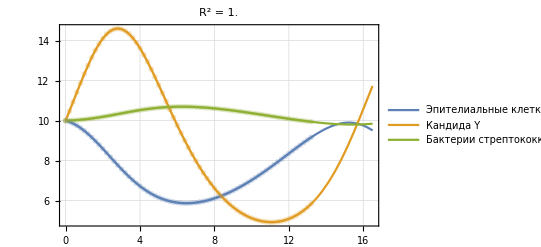

./Documents/Thesis/res/smoothed-trapez-plot.png

```mathematica
Show[
Plot[Evaluate[Nsolution[t]],{t,preData["t"]//Min,1.25preData["t"]//Max},PlotRange->{{0,All},{0,All}},Frame->True,GridLines->Automatic,PlotLegends->{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"},PlotStyle->Directive[Thick]],
ListPlot[Transpose[preData["X"][[;;;;5]]],PlotMarkers->{"OpenMarkers"},PlotStyle->Opacity[.3],
DataRange->{0,Last[preData["t"]]},Joined->True],
PlotLabel->StringForm["R^2 = ``",Mean[kmCoefficientR2Raw[Nsolution,Transpose@preData["X"],preData["t"]]]]
]
Export["./Documents/Thesis/res/smoothed-trapez-plot.png",%]
```

```mathematica
kmCoefficientR2[data["X"],data["Y"],A]
kmCoefficientR2Raw[Nsolution,Transpose@preData["X"],preData["t"]]
```

{1.,1.,1.}

{1.,1.,1.}

#### NsolutionInfty

{InterpolatingFunction[…][#1],InterpolatingFunction[…][#1],InterpolatingFunction[…][#1]}&

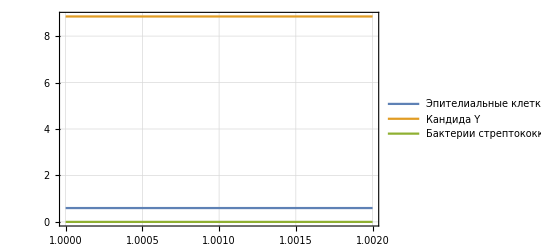

```mathematica
NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),{x1[0],x2[0],x3[0]}==First[preData["X"]]},{x1[t],x2[t],x3[t]},{t,10^7,1.002 10^7}];
NsolutionInfty=With[{$=Through[First[%[[All,All,2,0]]][#]]},$&]
Plot[Evaluate[NsolutionInfty[t]],{t,10^7,1.002 10^7},PlotRange->{{10^7,1.002 10^7},{0,All}},Frame->True,GridLines->Automatic,PlotStyle->Directive[Thick],PlotLegends->{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"}]
```

Piecewise[{{ⅆX/ⅆt=X(0.198                        -0.022StyleBox[\"\"\",ShowStringCharacters->False]Y), }, {ⅆY/ⅆt=Y(-0.056 "" +0.094X                     -0.065 Z), }, {ⅆZ/ⅆt=Z("-0.03"                        +0.003 Y), }}]

X=0.6
Y=8.8
Z=0.0

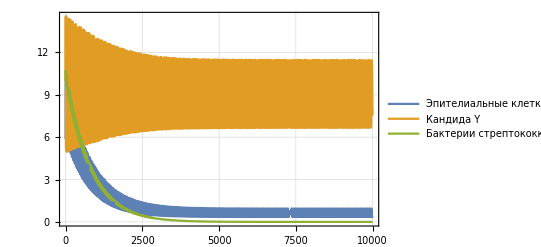

./Documents/Thesis/res/smoothed-trapez-semiinfty.png

```mathematica
NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),{x1[0],x2[0],x3[0]}==First[preData["X"]]},{x1[t],x2[t],x3[t]},{t,0.,1. 10^4}];
NsolutionInfty=With[{$=Through[First[%[[All,All,2,0]]][#]]},$&];
Plot[Evaluate[NsolutionInfty[t]],{t,0,1. 10^4},PlotRange->{{0,All},{0,All}},Frame->True,GridLines->Automatic,PlotStyle->Directive[Thick],PlotLegends->{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"}]
Export["./Documents/Thesis/res/smoothed-trapez-semiinfty.png",%]
```

```mathematica
(*NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),{x1[0],x2[0],x3[0]}==First[preData["X"]]},{x1[t],x2[t],x3[t]},{t,0.,1. 10^7}];
NsolutionInfty=With[{$=Through[First[%[[All,All,2,0]]][#]]},$&];
Plot[Evaluate[NsolutionInfty[t]],{t,0,1. 10^7},PlotRange->{{0,All},{0,All}},Frame->True,GridLines->Automatic,PlotStyle->Directive[Thick],PlotLegends->{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"}]*)
```

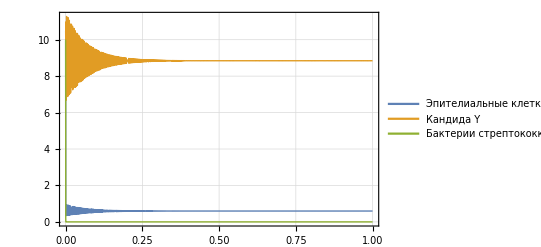

```mathematica
NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),{x1[0],x2[0],x3[0]}==First[preData["X"]]},{x1[t],x2[t],x3[t]},{t,1. 10^7,1. 10^7}];
NsolutionInfty=With[{$=Through[First[%[[All,All,2,0]]][#]]},$&];
NsolutionInfty[1. 10^7]
```

{0.596205,8.84514,4.7×10^-322}

# MacLaren

## Task

```mathematica
SetDirectory[NotebookDirectory[]]
path="./data/McLaren_1994";
files=Import[path];
```

/Users/danila/Documents/Thesis

```mathematica
PrepareRawData[data_,name_]:=Block[{time,value},
{time,value}=Transpose[N@Rest[data]];
StringReplace[name,".csv"->""]-><|
"measurement"->data[[1,2]],
"time"->time-Min[time],
"value"->value
|>
]
```

```mathematica
dataRaw=Association[PrepareRawData[Import[StringJoin[path,"/",#]],#]&/@ files]
```

<|fir→<|measurement→width,time→{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.},value→{0.462,0.465,0.465,0.461,0.451,0.366,0.413,0.481,0.49,0.628,0.608,0.594,0.53,0.516,0.455,0.448,0.458,0.36,0.255,0.225,0.224,0.315,0.325,0.365,0.446,0.591,0.681,0.597,0.624,0.651,0.542,0.529,0.427,0.329}|>,moose→<|measurement→individuals,time→{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.},value→{547.,558.,575.,591.,630.,673.,717.,849.,997.,1194.,1200.,1331.,1408.,1369.,1419.,1315.,1265.,1095.,964.,991.,904.,843.,800.,969.,898.,1024.,1046.,1002.,1358.,1643.,1375.,1205.,1304.,1572.}|>,wolf→<|measurement→individuals,time→{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.},value→{19.,21.,21.,22.,19.,25.,27.,25.,21.,21.,16.,17.,19.,22.,23.,30.,40.,44.,33.,39.,42.,49.,29.,12.,22.,23.,20.,19.,15.,11.,10.,14.,10.,10.}|>|>

```mathematica
preData=<|"title"->"McLaren_1994","measurements"->Values[#["measurement"]&/@dataRaw],"names"->Keys[dataRaw],"X"->Transpose[Values[#["value"]&/@dataRaw]],"t"->dataRaw[[1,"time"]],"N"->Length[dataRaw[[1,"time"]]]|>
```

<|title→McLaren_1994,measurements→{width,individuals,individuals},names→{fir,moose,wolf},X→{{0.462,547.,19.},{0.465,558.,21.},{0.465,575.,21.},{0.461,591.,22.},{0.451,630.,19.},{0.366,673.,25.},{0.413,717.,27.},{0.481,849.,25.},{0.49,997.,21.},{0.628,1194.,21.},{0.608,1200.,16.},{0.594,1331.,17.},{0.53,1408.,19.},{0.516,1369.,22.},{0.455,1419.,23.},{0.448,1315.,30.},{0.458,1265.,40.},{0.36,1095.,44.},{0.255,964.,33.},{0.225,991.,39.},{0.224,904.,42.},{0.315,843.,49.},{0.325,800.,29.},{0.365,969.,12.},{0.446,898.,22.},{0.591,1024.,23.},{0.681,1046.,20.},{0.597,1002.,19.},{0.624,1358.,15.},{0.651,1643.,11.},{0.542,1375.,10.},{0.529,1205.,14.},{0.427,1304.,10.},{0.329,1572.,10.}},t→{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.},N→34|>

## Model

{(ⅆ x_1)/ⅆt=x_1(b_1+∑_(i=1)^3 A_(i,1)x_i)
(ⅆ x_2)/ⅆt=x_2(b_2+∑_(i=1)^3 A_(i,2)x_i)
(ⅆ x_3)/ⅆt=x_3(b_3+∑_(i=1)^3 A_(i,3)x_i)

{ⅆLn[x_1]/ⅆt=b_1+∑_(i=1)^3 A_(i,1)x_i
ⅆLn[x_2]/ⅆt=b_2+∑_(i=1)^3 A_(i,2)x_i
ⅆLn[x_3]/ⅆt=b_3+∑_(i=1)^3 A_(i,3)x_i

## Метод Эйлера

## Замена

Применим метод Эйлера

{(Ln[x_1^(k+1)]-Ln[x_1^(k)])/Δt=b_1+∑_(i=1)^3 A_(i,1)x_i^(k)
(Ln[x_2^(k+1)]-Ln[x_2^(k)])/Δt=b_2+∑_(i=1)^3 A_(i,2)x_i^(k)
(Ln[x_3^(k+1)]-Ln[x_3^(k)])/Δt=b_3+∑_(i=1)^3 A_(i,3)x_i^(k), k=OverBar[1,N-1]

N – количество доступных наблюдений

Определим матрицы X,Y,A:

X_k=[1,x_1^(k),x_2^(k),x_3^(k)]– k-ая строка матрицы X

Y_k=[(Ln[x_1^(k+1)]-Ln[x_1^(k)])/Δt,(Ln[x_2^(k+1)]-Ln[x_2^(k)])/Δt,(Ln[x_3^(k+1)]-Ln[x_3^(k)])/Δt]– k-ая строка матрицы Y

k=OverBar[1,N-1]

A=(b_1 | b_2 | b_3
A_(1,1) | A_(1,2) | A_(1,3)
A_(2,1) | A_(2,2) | A_(2,3)
A_(3,1) | A_(3,2) | A_(3,3))

Тогда система примет вид

Y=X.A

## Подготовка данных

### data

```mathematica
data=Join[preData,
<|"X"->Most@Join[Transpose@{ConstantArray[1,preData["N"]]},preData["X"],2],
"Δt"->Differences[preData["t"]],
"Y"->Differences[Map[Log,preData["X"],{2}]]/Differences[preData["t"]]
|>];
```

## Подходы

### Обычный подход

```mathematica
data["X"];
data["Y"];
N@Inverse[Transpose[%%].%%].Transpose[%%].%//MatrixForm
```

(0.353242 | 0.405369 | 0.860336
-0.261509 | 0.12231 | -1.12785
-0.337344 | -0.535406 | 0.285184
-0.149878 | -0.326751 | -1.09996)

```mathematica
N@LeastSquares[data["X"],data["Y"]]//MatrixForm
```

(0.353242 | 0.405369 | 0.860336
-0.261509 | 0.12231 | -1.12785
-0.337344 | -0.535406 | 0.285184
-0.149878 | -0.326751 | -1.09996)

### Principle Components Regression (PCR)

```mathematica
PCR[data["X"],data["Y"],#]&/@Range[4];
Grid[Join[{{"A","||δy||"}},{MatrixForm[#],MatrixForm[Norm[data["Y"]-data["X"].#]/Norm[data["Y"]]]}&/@%],Frame->All]
```

A | ||δy||
(-0.0203245 | 0.0452986 | -0.0453336
-0.0123165 | 0.0274507 | -0.0274719
-0.0105764 | 0.0235724 | -0.0235906
-0.00749612 | 0.0167071 | -0.0167201) | 0.990649
(0.0316126 | 0.0377334 | -0.0685057
-0.133881 | 0.0451577 | 0.0267651
-0.086609 | 0.0346473 | 0.0103319
0.158698 | -0.00750064 | -0.0908688) | 0.989925
(0.133559 | 0.250495 | -0.113242
-0.0129492 | 0.297543 | -0.0263027
-0.371185 | -0.559263 | 0.135211
0.0851044 | -0.16109 | -0.0585742) | 0.987961
(0.353242 | 0.405369 | 0.860336
-0.261509 | 0.12231 | -1.12785
-0.337344 | -0.535406 | 0.285184
-0.149878 | -0.326751 | -1.09996) | 0.935722

### Partial least squares regression (PLSR)

```mathematica
data["X"];
data["Y"];
PLSR[%%,%,#]&/@Range[4];
Grid[Join[{{"A","||δy||"}},{MatrixForm[#],MatrixForm[Norm[%%-%%%.#]/Norm[%%]]}&/@%],Frame->All]
```

A | ||δy||
(-0.0193433 | 0.0459243 | -0.0457441
-0.0152555 | 0.0362191 | -0.036077
-0.00704192 | 0.0167187 | -0.0166531
-0.0078427 | 0.0186199 | -0.0185469) | 0.990038
(0.123695 | 0.190897 | -0.116565
0.0258562 | 0.0778868 | -0.0564321
-0.3882 | -0.369594 | 0.172065
0.0702382 | 0.0977568 | -0.0572061) | 0.986907
(0.123512 | 0.337148 | -0.0464345
0.0256938 | 0.207599 | 0.00576724
-0.387973 | -0.55044 | 0.0853455
0.0706877 | -0.261251 | -0.229358) | 0.985252
(0.353242 | 0.405369 | 0.860336
-0.261509 | 0.12231 | -1.12785
-0.337344 | -0.535406 | 0.285184
-0.149878 | -0.326751 | -1.09996) | 0.935722

## Решение

### A

(0.353242 | 0.405369 | 0.860336
-0.261509 | 0.12231 | -1.12785
-0.337344 | -0.535406 | 0.285184
-0.149878 | -0.326751 | -1.09996)

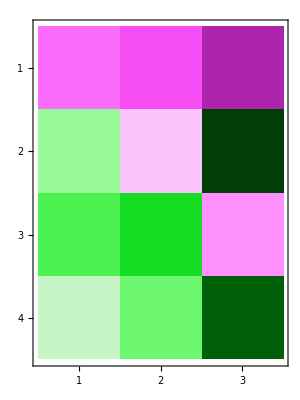

```mathematica
data["X"];
data["Y"];
(A=PLSR[%%,%,4])//MatrixForm
MatrixPlot[%,ColorFunction->"GreenPinkTones"]
```

```mathematica
Grid[Join[Transpose@{Join[{"","const"},data["names"]]},Join[{data["names"]},A],2],Frame->All]
```

| fir | moose | wolf
const | 0.353242 | 0.405369 | 0.860336
fir | -0.261509 | 0.12231 | -1.12785
moose | -0.337344 | -0.535406 | 0.285184
wolf | -0.149878 | -0.326751 | -1.09996

```mathematica
Grid[Join[Transpose@{Join[{"","const"},data["names"]]},Join[{data["names"]},Transpose@kmConfidenceInterval[data["X"],data["Y"],A]],2],Frame->All]
```

| fir | moose | wolf
const | 0.35324 (±0.286) | 0.40537 (±0.0456) | 0.86034 (±0.632)
fir | -0.26151 (±0.39) | 0.12231 (±0.0622) | -1.12790 (±0.861)
moose | -0.33734 (±0.218) | -0.53541 (±0.0348) | 0.28518 (±0.482)
wolf | -0.14988 (±0.36) | -0.32675 (±0.0574) | -1.10000 (±0.795)

```mathematica
kmCoefficientR2[data["X"],data["Y"],A]
```

{0.0736984,0.434443,0.115098}

### Сравнение

#### Решение (встроенное)

{(ⅆ x_1)/ⅆt=x_1(b_1+∑_(i=1)^3 A_(i,1)x_i)
(ⅆ x_2)/ⅆt=x_2(b_2+∑_(i=1)^3 A_(i,2)x_i)
(ⅆ x_3)/ⅆt=x_3(b_3+∑_(i=1)^3 A_(i,3)x_i)

```mathematica
startTime=preData["t"]//Min;
NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),{x1[startTime],x2[startTime],x3[startTime]}==Rest@First[data["X"]]},{x1[t],x2[t],x3[t]},{t,preData["t"]//Min,preData["t"]//Max}];
Nsolution=With[{$=Through[First[%[[All,All,2,0]]][#]]},$&]
```

{InterpolatingFunction[…][#1],InterpolatingFunction[…][#1],InterpolatingFunction[…][#1]}&

#### Graph

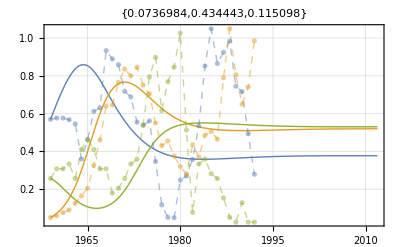

```mathematica
Show[
Plot[Evaluate[Nsolution[t]],{t,preData["t"]//Min,1.01preData["t"]//Max},PlotRange->{{startTime,All},{0,All}},Frame->True,GridLines->Automatic,PlotStyle->Directive[Thick]],
ListPlot[Transpose[preData["X"]],Joined->True,DataRange->{startTime,Last[preData["t"]]},PlotStyle->Directive[Dashed,Thick,Opacity[0.5]],Mesh->All],PlotLabel->kmCoefficientR2[data["X"],data["Y"],A]
]
```

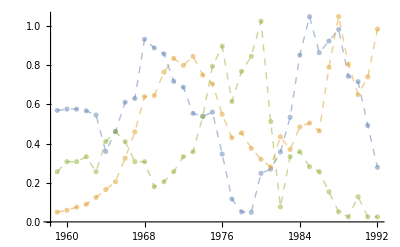

```mathematica
ListPlot[Transpose[preData["X"]],Joined->True,DataRange->{startTime,Last[preData["t"]]},PlotStyle->Directive[Dashed,Thick,Opacity[0.5]],Mesh->All]
```

## Метод Трапеции

## Замена

Применим метод Трапеции

{(Ln[x_1^(k+1)]-Ln[x_1^(k)])/Δt=b_1+∑_(i=1)^3 A_(i,1)(x_i^(k+1)+x_i^(k))/2
(Ln[x_2^(k+1)]-Ln[x_2^(k)])/Δt=b_2+∑_(i=1)^3 A_(i,2)(x_i^(k+1)+x_i^(k))/2
(Ln[x_3^(k+1)]-Ln[x_3^(k)])/Δt=b_3+∑_(i=1)^3 A_(i,3)(x_i^(k+1)+x_i^(k))/2, k=OverBar[1,N-1]

N – количество доступных наблюдений

Определим матрицы X,Y,A:

X_k=[1,(x_1^(k+1)+x_1^(k))/2,(x_2^(k+1)+x_2^(k))/2,(x_3^(k+1)+x_3^(k))/2]– k-ая строка матрицы X

Y_k=[(Ln[x_1^(k+1)]-Ln[x_1^(k)])/Δt,(Ln[x_2^(k+1)]-Ln[x_2^(k)])/Δt,(Ln[x_3^(k+1)]-Ln[x_3^(k)])/Δt]– k-ая строка матрицы Y

k=OverBar[1,N-1]

A=(b_1 | b_2 | b_3
A_(1,1) | A_(1,2) | A_(1,3)
A_(2,1) | A_(2,2) | A_(2,3)
A_(3,1) | A_(3,2) | A_(3,3))

Тогда система примет вид

Y=X.A

## Подготовка данных

### data

```mathematica
data=Join[preData,
<|"X"->(Most[#]+Rest[#])/2&[Join[Transpose@{ConstantArray[1,preData["N"]]},preData["X"],2]],
"Δt"->Differences[preData["t"]],
"Y"->Differences[Map[Log,preData["X"],{2}]]/Differences[preData["t"]]
|>];
```

## Подходы

### Обычный подход

```mathematica
data["X"];
data["Y"];
N@Inverse[Transpose[%%].%%].Transpose[%%].%//MatrixForm
```

(-0.111919 | 0.232543 | -0.0639458
0.47825 | 0.0292328 | -0.112454
-0.000202662 | -0.0000846883 | 0.0000633911
0.00387358 | -0.00533864 | 0.00129793)

```mathematica
N@LeastSquares[data["X"],data["Y"]]//MatrixForm
```

(-0.111919 | 0.232543 | -0.0639458
0.47825 | 0.0292328 | -0.112454
-0.000202662 | -0.0000846883 | 0.0000633911
0.00387358 | -0.00533864 | 0.00129793)

### Principle Components Regression (PCR)

```mathematica
PCR[data["X"],data["Y"],#]&/@Range[4];
Grid[Join[{{"A","||δy||"}},{MatrixForm[#],MatrixForm[Norm[data["Y"]-data["X"].#]/Norm[data["Y"]]]}&/@%],Frame->All]
```

A | ||δy||
(-1.8135×10^-8 | 2.35248×10^-8 | -1.33499×10^-8
-8.67602×10^-9 | 1.12546×10^-8 | -6.38674×10^-9
-0.0000204007 | 0.0000264638 | -0.0000150177
-4.12652×10^-7 | 5.35293×10^-7 | -3.03769×10^-7) | 0.996718
(0.0000361055 | -0.0000280145 | 4.46094×10^-6
1.16912×10^-6 | -9.02911×10^-7 | 1.39495×10^-7
-0.0000702714 | 0.0000651718 | -0.0000211947
0.00246348 | -0.00191186 | 0.000304875) | 0.996173
(0.138436 | 0.177766 | -0.096389
0.0890457 | 0.114389 | -0.0620178
-0.000189217 | -0.0000876301 | 0.0000616487
0.00038939 | -0.00457632 | 0.00174944) | 0.989695
(-0.111919 | 0.232543 | -0.0639458
0.47825 | 0.0292328 | -0.112454
-0.000202662 | -0.0000846883 | 0.0000633911
0.00387358 | -0.00533864 | 0.00129793) | 0.989683

### Partial least squares regression (PLSR)

```mathematica
data["X"];
data["Y"];
PLSR[%%,%,#]&/@Range[4];
Grid[Join[{{"A","||δy||"}},{MatrixForm[#],MatrixForm[Norm[%%-%%%.#]/Norm[%%]]}&/@%],Frame->All]
```

A | ||δy||
(-1.73892×10^-8 | 2.25558×10^-8 | -1.2799×10^-8
-9.32271×10^-9 | 1.20926×10^-8 | -6.86183×10^-9
-0.0000204085 | 0.0000264721 | -0.0000150213
-1.98386×10^-7 | 2.57329×10^-7 | -1.46019×10^-7) | 0.996717
(0.0000287433 | -0.0000223001 | 3.54831×10^-6
7.89724×10^-6 | -6.12461×10^-6 | 9.72118×10^-7
-0.0000702698 | 0.0000651722 | -0.0000211951
0.00246359 | -0.00191202 | 0.000304917) | 0.996173
(0.13455 | 0.168881 | -0.0922147
0.100918 | 0.126696 | -0.069176
-0.000191849 | -0.0000874814 | 0.0000621509
0.000440693 | -0.00445194 | 0.00169167) | 0.989686
(-0.111919 | 0.232543 | -0.0639458
0.47825 | 0.0292328 | -0.112454
-0.000202662 | -0.0000846883 | 0.0000633911
0.00387358 | -0.00533864 | 0.00129793) | 0.989683

## Решение

### A

(-0.111919 | 0.232543 | -0.0639458
0.47825 | 0.0292328 | -0.112454
-0.000202662 | -0.0000846883 | 0.0000633911
0.00387358 | -0.00533864 | 0.00129793)

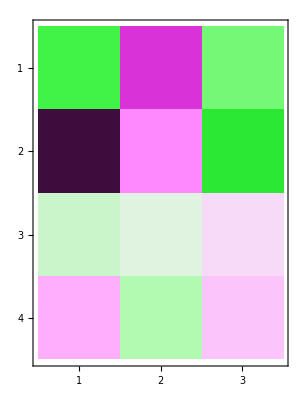

```mathematica
data["X"];
data["Y"];
(A=PLSR[%%,%,4])//MatrixForm
MatrixPlot[%,ColorFunction->"GreenPinkTones"]
```

#### tables

```mathematica
Grid[Join[Transpose@{Join[{"","const"},data["names"]]},Join[{data["names"]},A],2],Frame->All]
```

| fir | moose | wolf
const | -0.111919 | 0.232543 | -0.0639458
fir | 0.47825 | 0.0292328 | -0.112454
moose | -0.000202662 | -0.0000846883 | 0.0000633911
wolf | 0.00387358 | -0.00533864 | 0.00129793

```mathematica
Grid[Join[Transpose@{Join[{"","const"},data["names"]]},Join[{data["names"]},Transpose@kmConfidenceInterval[data["X"],data["Y"],A]],2],Frame->All]
```

| fir | moose | wolf
const | -0.11192 (±0.115) | 0.23254 (±0.0574) | -0.06395 (±0.398)
fir | 0.47825 (±0.234) | 0.02923 (±0.117) | -0.11245 (±0.809)
moose | -0.00020 (±2.15×10^-8) | -0.00008 (±1.07×10^-8) | 0.00006 (±7.42×10^-8)
wolf | 0.00387 (±0.0000322) | -0.00534 (±0.0000161) | 0.00130 (±0.000111)

```mathematica
data["names"];
Grid[Join[Transpose@{Join[{"","const"},%]},Join[{%},A],2],Frame->All]
```

| fir | moose | wolf
const | -0.111919 | 0.232543 | -0.0639458
fir | 0.47825 | 0.0292328 | -0.112454
moose | -0.000202662 | -0.0000846883 | 0.0000633911
wolf | 0.00387358 | -0.00533864 | 0.00129793

```mathematica
Join[A,Table[StringForm["a_(``, ``)",i,j],{i,0,3},{j,1,3}],2][[All,{4,1,5,2,6,3}]];
data["names"];
Grid[Join[Transpose@{Join[{"","const"},%]},Join[{Riffle[%,SpanFromLeft,{2,-1,2}]},%%],2],Frame->All]
```

| fir |  | moose |  | wolf | 
const | a_(RowBox[{) | -0.111919 | a_(RowBox[{) | 0.232543 | a_(RowBox[{) | -0.0639458
fir | a_(RowBox[{) | 0.47825 | a_(RowBox[{) | 0.0292328 | a_(RowBox[{) | -0.112454
moose | a_(RowBox[{) | -0.000202662 | a_(RowBox[{) | -0.0000846883 | a_(RowBox[{) | 0.0000633911
wolf | a_(RowBox[{) | 0.00387358 | a_(RowBox[{) | -0.00533864 | a_(RowBox[{) | 0.00129793

```mathematica
Join[Transpose@kmConfidenceInterval[data["X"],data["Y"],A],Table[StringForm["a_(``, ``)",i,j],{i,0,3},{j,1,3}],2][[All,{4,1,5,2,6,3}]];
data["names"];
Grid[Join[Transpose@{Join[{"","const"},%]},Join[{Riffle[%,SpanFromLeft,{2,-1,2}]},%%],2],Frame->All,Alignment->{{Center},{Left}}]
```

| fir |  | moose |  | wolf | 
const | a_(RowBox[{) | -0.11192 (±0.115) | a_(RowBox[{) | 0.23254 (±0.0574) | a_(RowBox[{) | -0.06395 (±0.398)
fir | a_(RowBox[{) | 0.47825 (±0.234) | a_(RowBox[{) | 0.02923 (±0.117) | a_(RowBox[{) | -0.11245 (±0.809)
moose | a_(RowBox[{) | -0.00020 (±2.15×10^-8) | a_(RowBox[{) | -0.00008 (±1.07×10^-8) | a_(RowBox[{) | 0.00006 (±7.42×10^-8)
wolf | a_(RowBox[{) | 0.00387 (±0.0000322) | a_(RowBox[{) | -0.00534 (±0.0000161) | a_(RowBox[{) | 0.00130 (±0.000111)

#### system

```mathematica
DecimalForm[Thread[Rule[Flatten@Table[StringForm["a_(````)",i,j],{i,0,3},{j,1,3}],Flatten@A]],{3,3}]
```

{SubscriptBox[a, RowBox[{"\"0\""}]RowBox[{"\"1\""}]]→-0.112,SubscriptBox[a, RowBox[{"\"0\""}]RowBox[{"\"2\""}]]→0.233,SubscriptBox[a, RowBox[{"\"0\""}]RowBox[{"\"3\""}]]→-0.064,SubscriptBox[a, RowBox[{"\"1\""}]RowBox[{"\"1\""}]]→0.478,SubscriptBox[a, RowBox[{"\"1\""}]RowBox[{"\"2\""}]]→0.029,SubscriptBox[a, RowBox[{"\"1\""}]RowBox[{"\"3\""}]]→-0.112,SubscriptBox[a, RowBox[{"\"2\""}]RowBox[{"\"1\""}]]→-0.000,SubscriptBox[a, RowBox[{"\"2\""}]RowBox[{"\"2\""}]]→-0.000,SubscriptBox[a, RowBox[{"\"2\""}]RowBox[{"\"3\""}]]→0.000,SubscriptBox[a, RowBox[{"\"3\""}]RowBox[{"\"1\""}]]→0.004,SubscriptBox[a, RowBox[{"\"3\""}]RowBox[{"\"2\""}]]→-0.005,SubscriptBox[a, RowBox[{"\"3\""}]RowBox[{"\"3\""}]]→0.001}

Piecewise[{{ⅆX/ⅆt=X(0.198                        -0.022""Y), }, {ⅆY/ⅆt=Y(-0.056 "" +0.094X                     -0.065 Z), }, {ⅆZ/ⅆt=Z("-0.03"                        +0.003 Y), }}]

### Сравнение

#### Решение (встроенное)

{(ⅆ X_1)/ⅆt=x_1(b_1+∑_(i=1)^3 A_(i,1)x_i)
(ⅆ x_2)/ⅆt=x_2(b_2+∑_(i=1)^3 A_(i,2)x_i)
(ⅆ x_3)/ⅆt=x_3(b_3+∑_(i=1)^3 A_(i,3)x_i)

```mathematica
startTime=data["t"]//Min;
NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),{x1[0],x2[0],x3[0]}==First[preData["X"]]},{x1[t],x2[t],x3[t]},{t,0,data["t"]//Max}];
Nsolution=With[{$=Through[First[%[[All,All,2,0]]][#]]},$&]
```

NDSolve::ndsz: At t == 13.1779, step size is effectively zero; singularity or stiff system suspected.

{InterpolatingFunction[…][#1],InterpolatingFunction[…][#1],InterpolatingFunction[…][#1]}&

#### Graph

```mathematica
Show[
Plot[Evaluate[Nsolution[t]],{t,preData["t"]//Min,1.25preData["t"]//Max},PlotRange->{{0,All},{0,All}},Frame->True,GridLines->Automatic,PlotStyle->Directive[Thick]],
ListPlot[Transpose[preData["X"]],PlotMarkers->"x",PlotStyle->Thick,DataRange->{0,Last[preData["t"]]},Joined->True,PlotStyle->Directive[Dashed,Thick,Opacity[0.5]],Mesh->All],
PlotLabel->kmCoefficientR2[data["X"],data["Y"],A]
]
```

-Graphics-

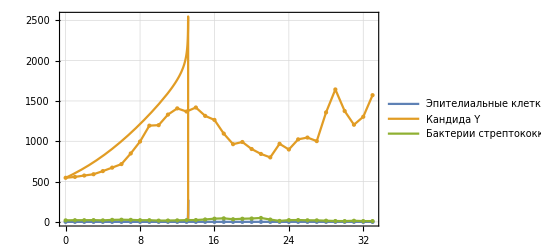

```mathematica
Show[
Plot[Evaluate[Nsolution[t]],{t,preData["t"]//Min,1.25preData["t"]//Max},PlotRange->{{0,All},{0,All}},Frame->True,GridLines->Automatic,PlotStyle->Directive[Thick],PlotLegends->{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"}],
ListPlot[Transpose[preData["X"]],PlotStyle->PointSize[Medium],DataRange->{0,Last[preData["t"]]},Joined->True,PlotStyle->Directive[Dashed,Thick,Opacity[0.5]],Mesh->All]
]
```

```mathematica
kmCoefficientR2[data["X"],data["Y"],A]
```

{0.148176,0.19708,0.0074803}

```mathematica
Mean[kmCoefficientR2[data["X"],data["Y"],A]]
```

0.117579

#### NsolutionInfty

NDSolve::ndsz: At t == 13.1779, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 1.×10^7 and t == 1.002×10^7.

First::nofirst: {} has zero length and no first element.

#1&

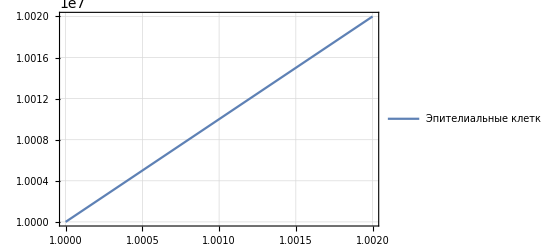

```mathematica
NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),{x1[0],x2[0],x3[0]}==First[preData["X"]]},{x1[t],x2[t],x3[t]},{t,10^7,1.002 10^7}];
NsolutionInfty=With[{$=Through[First[%[[All,All,2,0]]][#]]},$&]
Plot[Evaluate[NsolutionInfty[t]],{t,10^7,1.002 10^7},PlotRange->{{10^7,1.002 10^7},{0,All}},Frame->True,GridLines->Automatic,PlotStyle->Directive[Thick],PlotLegends->{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"}]
```

Piecewise[{{ⅆX/ⅆt=X(0.198                        -0.022"""Y), }, {ⅆY/ⅆt=Y(-0.056 "" +0.094X                     -0.065 Z), }, {ⅆZ/ⅆt=Z("-0.03"                        +0.003 Y), }}]

X=0.6
Y=8.8
Z=0.0

# L-V experimental data PATHOG.csv

## Task

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danila/Documents/Thesis

```mathematica
dataRaw=Import["./data/L-V experimental data PATHOG.csv"];
```

```mathematica
dataRaw
```

{{hours,Epithel,Commensual,Pathog},{0,21.7708,98.3717,29.7805},{6,20.4758,10.5609,31.067},{12,67.4628,36.261,20.5365},{18,22.5021,30.789,36.6855},{24,58.4723,6.42626,55.4899},{36,66.884,58.2325,28.5071},{48,24.2639,26.1348,46.9728}}

### preData

```mathematica
Rest[dataRaw];
preData=<|"title"->"L-V experimental data PATHOG","names"->Rest@First[dataRaw],"X"->%[[All,2;;]],"t"->%[[All,1]],"N"->Length[%]|>
```

<|title→L-V experimental data PATHOG,names→{Epithel,Commensual,Pathog},X→{{21.7708,98.3717,29.7805},{20.4758,10.5609,31.067},{67.4628,36.261,20.5365},{22.5021,30.789,36.6855},{58.4723,6.42626,55.4899},{66.884,58.2325,28.5071},{24.2639,26.1348,46.9728}},t→{0,6,12,18,24,36,48},N→7|>

## Метод Эйлера

## Замена

Применим метод Эйлера

{(Ln[x_1^(k+1)]-Ln[x_1^(k)])/Δt=b_1+∑_(i=1)^3 A_(i,1)x_i^(k)
(Ln[x_2^(k+1)]-Ln[x_2^(k)])/Δt=b_2+∑_(i=1)^3 A_(i,2)x_i^(k)
(Ln[x_3^(k+1)]-Ln[x_3^(k)])/Δt=b_3+∑_(i=1)^3 A_(i,3)x_i^(k), k=OverBar[1,N-1]

N – количество доступных наблюдений

Определим матрицы X,Y,A:

X_k=[1,x_1^(k),x_2^(k),x_3^(k)]– k-ая строка матрицы X

Y_k=[(Ln[x_1^(k+1)]-Ln[x_1^(k)])/Δt,(Ln[x_2^(k+1)]-Ln[x_2^(k)])/Δt,(Ln[x_3^(k+1)]-Ln[x_3^(k)])/Δt]– k-ая строка матрицы Y

k=OverBar[1,N-1]

A=(b_1 | b_2 | b_3
A_(1,1) | A_(1,2) | A_(1,3)
A_(2,1) | A_(2,2) | A_(2,3)
A_(3,1) | A_(3,2) | A_(3,3))

Тогда система примет вид

Y=X.A

## Подготовка данных

### data

```mathematica
data=Join[preData,
<|"X"->Most@Join[Transpose@{ConstantArray[1,preData["N"]]},preData["X"],2],
"Δt"->Differences[preData["t"]],
"Y"->Differences[Map[Log,preData["X"],{2}]]/Differences[preData["t"]]
|>];
```

```mathematica
data
```

<|title→L-V experimental data PATHOG,names→{Epithel,Commensual,Pathog},X→{{1,21.7708,98.3717,29.7805},{1,20.4758,10.5609,31.067},{1,67.4628,36.261,20.5365},{1,22.5021,30.789,36.6855},{1,58.4723,6.42626,55.4899},{1,66.884,58.2325,28.5071}},t→{0,6,12,18,24,36,48},N→7,Δt→{6,6,6,6,12,12},Y→{{-0.0102216,-0.371933,0.00704884},{0.198722,0.205598,-0.0689901},{-0.182995,-0.0272643,0.096696},{0.159157,-0.261127,0.0689698},{0.0112006,0.183671,-0.0555039},{-0.0844976,-0.0667646,0.0416179}}|>

## Подходы

### Обычный подход

```mathematica
data["X"];
data["Y"];
N@Inverse[Transpose[%%].%%].Transpose[%%].%//MatrixForm
```

(0.257268 | 0.0834268 | 0.0576156
-0.00531187 | 0.0021868 | 0.000933082
-0.00179925 | -0.00545191 | 0.000320827
0.00172665 | -0.000443794 | -0.00283764)

```mathematica
N@LeastSquares[data["X"],data["Y"]]//MatrixForm
```

(0.257268 | 0.0834268 | 0.0576156
-0.00531187 | 0.0021868 | 0.000933082
-0.00179925 | -0.00545191 | 0.000320827
0.00172665 | -0.000443794 | -0.00283764)

### Principle Components Regression (PCR)

```mathematica
PCR[data["X"],data["Y"],#]&/@Range[4];
Grid[Join[{{"A","||δy||"}},{MatrixForm[#],MatrixForm[Norm[data["Y"]-data["X"].#]/Norm[data["Y"]]]}&/@%],Frame->All]
```

A | ||δy||
(-0.0000709792 | -0.000136218 | 4.75304×10^-6
-0.000527428 | -0.0010122 | 0.0000353186
-0.000686273 | -0.00131704 | 0.0000459555
-0.000736071 | -0.00141261 | 0.0000492902) | 0.972536
(0.00127485 | -0.000238937 | -0.000190815
0.008955 | -0.00173593 | -0.00134261
-0.0226695 | 0.000360799 | 0.00324042
0.0128356 | -0.00244845 | -0.00192285) | 0.967615
(0.00154453 | -0.00441179 | -0.000231133
0.00283418 | 0.0929768 | -0.000427504
-0.0226264 | -0.000306121 | 0.00323398
0.0171552 | -0.0692902 | -0.00256867) | 0.00545046
(0.226628 | -0.0280342 | -0.0337612
-0.000868391 | 0.0933654 | 0.000124056
-0.0223593 | -0.000334157 | 0.00319419
-0.00214558 | -0.0672646 | 0.000306511) | 0.00124679

### Partial least squares regression (PLSR)

```mathematica
data["X"];
data["Y"];
PLSR[%%,%,#]&/@Range[4];
Grid[Join[{{"A","||δy||"}},{MatrixForm[#],MatrixForm[Norm[%%-%%%.#]/Norm[%%]]}&/@%],Frame->All]
```

A | ||δy||
(-0.0000790996 | -0.00014456 | 5.9048×10^-6
-0.000299117 | -0.000546658 | 0.0000223291
-0.000913191 | -0.00166892 | 0.0000681699
-0.000877732 | -0.00160412 | 0.0000655229) | 0.969722
(0.00142301 | -0.000439749 | -0.00021312
0.00573869 | -0.00173318 | -0.000858049
-0.022716 | 0.00261568 | 0.00324726
0.0151762 | -0.00475897 | -0.00227531) | 0.956989
(0.00154484 | -0.00441222 | -0.000231178
0.00283417 | 0.0929768 | -0.000427504
-0.0226264 | -0.000306121 | 0.00323398
0.0171552 | -0.0692902 | -0.00256867) | 0.00545046
(0.226628 | -0.0280342 | -0.0337612
-0.000868391 | 0.0933654 | 0.000124056
-0.0223593 | -0.000334157 | 0.00319419
-0.00214558 | -0.0672646 | 0.000306511) | 0.00124679

## Решение

### A

(0.257268 | 0.0834268 | 0.0576156
-0.00531187 | 0.0021868 | 0.000933082
-0.00179925 | -0.00545191 | 0.000320827
0.00172665 | -0.000443794 | -0.00283764)

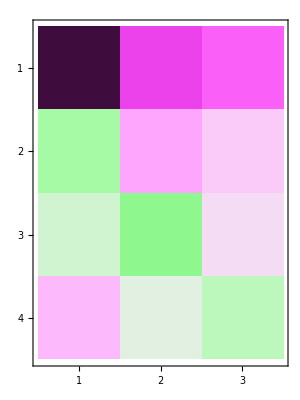

```mathematica
data["X"];
data["Y"];
(A=PLSR[%%,%,4])//MatrixForm
MatrixPlot[%,ColorFunction->"GreenPinkTones"]
```

```mathematica
Grid[Join[Transpose@{Join[{"","const"},data["names"]]},Join[{data["names"]},A],2],Frame->All]
```

| Epithel | Commensual | Pathog
const | 0.257268 | 0.0834268 | 0.0576156
Epithel | -0.00531187 | 0.0021868 | 0.000933082
Commensual | -0.00179925 | -0.00545191 | 0.000320827
Pathog | 0.00172665 | -0.000443794 | -0.00283764

```mathematica
Grid[Join[Transpose@{Join[{"","const"},data["names"]]},Join[{data["names"]},Transpose@kmConfidenceInterval[data["X"],data["Y"],A]],2],Frame->All]
```

| Epithel | Commensual | Pathog
const | 0.25727 (±0.0876) | 0.08343 (±0.712) | 0.05762 (±0.118)
Epithel | -0.00531 (±7.15×10^-6) | 0.00219 (±0.0000581) | 0.00093 (±9.64×10^-6)
Commensual | -0.00180 (±4.39×10^-6) | -0.00545 (±0.0000356) | 0.00032 (±5.91×10^-6)
Pathog | 0.00173 (±0.0000355) | -0.00044 (±0.000289) | -0.00284 (±0.0000479)

```mathematica
kmCoefficientR2[data["X"],data["Y"],A]
```

{0.913791,0.728171,0.458484}

```mathematica
Join[Transpose@kmConfidenceInterval[data["X"],data["Y"],A],Table[StringForm["a_(``, ``)",i,j],{i,0,3},{j,1,3}],2][[All,{4,1,5,2,6,3}]];
{"Эпителиальные клетки X", "Комменсал Y","Патоген Z"};
Grid[Join[Transpose@{Join[{"","Естественный рост"},%]},Join[{Riffle[%,SpanFromLeft,{2,-1,2}]},%%],2],Frame->All,Alignment->{{Center},{Left}}]
Export["./Documents/Thesis/res/pathogen-euler.png",%]
```

| Эпителиальные клетки X |  | Комменсал Y |  | Патоген Z | 
Естественный рост | a_(RowBox[{) | 0.25727 (±0.0876) | a_(RowBox[{) | 0.08343 (±0.712) | a_(RowBox[{) | 0.05762 (±0.118)
Эпителиальные клетки X | a_(RowBox[{) | -0.00531 (±7.15×10^-6) | a_(RowBox[{) | 0.00219 (±0.0000581) | a_(RowBox[{) | 0.00093 (±9.64×10^-6)
Комменсал Y | a_(RowBox[{) | -0.00180 (±4.39×10^-6) | a_(RowBox[{) | -0.00545 (±0.0000356) | a_(RowBox[{) | 0.00032 (±5.91×10^-6)
Патоген Z | a_(RowBox[{) | 0.00173 (±0.0000355) | a_(RowBox[{) | -0.00044 (±0.000289) | a_(RowBox[{) | -0.00284 (±0.0000479)

./Documents/Thesis/res/pathogen-euler.png

### Сравнение

#### Решение (встроенное)

{(ⅆ x_1)/ⅆt=x_1(b_1+∑_(i=1)^3 A_(i,1)x_i)
(ⅆ x_2)/ⅆt=x_2(b_2+∑_(i=1)^3 A_(i,2)x_i)
(ⅆ x_3)/ⅆt=x_3(b_3+∑_(i=1)^3 A_(i,3)x_i)

```mathematica
NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),{x1[0],x2[0],x3[0]}==Rest@First[data["X"]]},{x1[t],x2[t],x3[t]},{t,preData["t"]//Min,1.25preData["t"]//Max}];
Nsolution=With[{$=Through[First[%[[All,All,2,0]]][#]]},$&]
```

{InterpolatingFunction[…][#1],InterpolatingFunction[…][#1],InterpolatingFunction[…][#1]}&

#### Graph

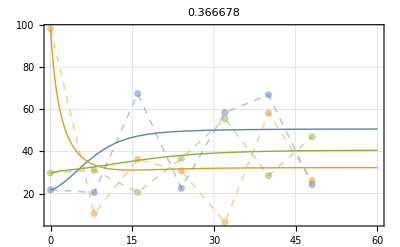

```mathematica
Show[
Plot[Evaluate[Nsolution[t]],{t,preData["t"]//Min,1.25preData["t"]//Max},PlotRange->{{0,All},{0,All}},Frame->True,GridLines->Automatic,PlotStyle->Directive[Thick]],
ListPlot[Transpose[preData["X"]],Joined->True,DataRange->{0,Last[preData["t"]]},PlotStyle->Directive[Dashed,Thick,Opacity[0.5]],Mesh->All],PlotLabel->Mean[kmCoefficientR2Raw[Nsolution,Transpose@preData["X"],preData["t"]]]
]
```

```mathematica
Transpose[preData["X"][[;;;;5]]]
```

{{21.7708,66.884},{98.3717,58.2325},{29.7805,28.5071}}

```mathematica
Transpose[{preData["t"],#}]&/@(Transpose[preData["X"]])
```

{{{0,21.7708},{6,20.4758},{12,67.4628},{18,22.5021},{24,58.4723},{36,66.884},{48,24.2639}},{{0,98.3717},{6,10.5609},{12,36.261},{18,30.789},{24,6.42626},{36,58.2325},{48,26.1348}},{{0,29.7805},{6,31.067},{12,20.5365},{18,36.6855},{24,55.4899},{36,28.5071},{48,46.9728}}}

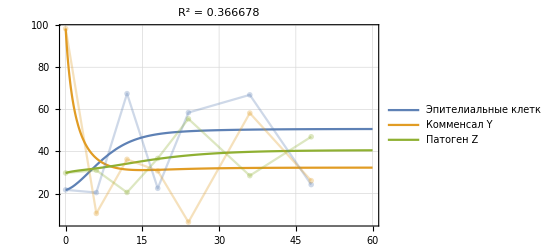

./Documents/Thesis/res/pathogen-euler-plot.png

```mathematica
Show[
Plot[Evaluate[Nsolution[t]],{t,preData["t"]//Min,1.25preData["t"]//Max},PlotRange->{{0,All},{0,All}},Frame->True,GridLines->Automatic,PlotLegends->{"Эпителиальные клетки X", "Комменсал Y","Патоген Z"},PlotStyle->Directive[Thick]],
ListPlot[Transpose[{preData["t"],#}]&/@(Transpose[preData["X"]]),PlotMarkers->{"OpenMarkers"},PlotStyle->Opacity[.3],
DataRange->{0,Last[preData["t"]]},Joined->True],
PlotLabel->StringForm["R^2 = ``",Mean[kmCoefficientR2Raw[Nsolution,Transpose@preData["X"],preData["t"]]]]
]
Export["./Documents/Thesis/res/pathogen-euler-plot.png",%]
```

```mathematica
kmCoefficientR2[data["X"],data["Y"],A]
kmCoefficientR2Raw[Nsolution,Transpose@preData["X"],preData["t"]]
```

{0.913791,0.728171,0.458484}

{0.214075,0.655702,0.230258}

#### infty

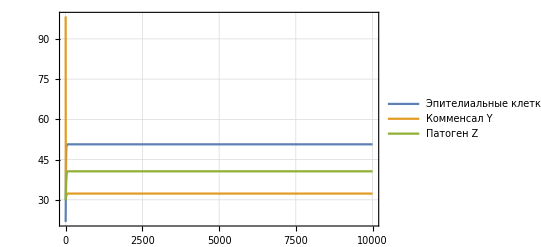

./Documents/Thesis/res/pathogen-euler-semiinfty.png

```mathematica
NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),{x1[0],x2[0],x3[0]}==First[preData["X"]]},{x1[t],x2[t],x3[t]},{t,0.,1. 10^4}];
NsolutionInfty=With[{$=Through[First[%[[All,All,2,0]]][#]]},$&];
Plot[Evaluate[NsolutionInfty[t]],{t,0,1. 10^4},PlotRange->{{0,All},{0,All}},Frame->True,GridLines->Automatic,PlotStyle->Directive[Thick],PlotLegends->{"Эпителиальные клетки X", "Комменсал Y","Патоген Z"}]
Export["./Documents/Thesis/res/pathogen-euler-semiinfty.png",%]
```

```mathematica
NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),{x1[0],x2[0],x3[0]}==First[preData["X"]]},{x1[t],x2[t],x3[t]},{t,1. 10^7,1. 10^7}];
NsolutionInfty=With[{$=Through[First[%[[All,All,2,0]]][#]]},$&];
NsolutionInfty[1. 10^7]
```

{50.6888,32.3269,40.6267}

X=50.7
Y=32.3
Z=40.6